```mathematica
$Assumptions = {Vg ∈ Reals, V0 ∈ Reals, κ ∈ Reals, a ∈ Reals, n ∈ Integers, Subscript[k, F] ∈ Reals}
```

{Vg∈ℝ,V0∈ℝ,κ∈ℝ,a∈ℝ,n∈ℤ,k_F∈ℝ}

```mathematica
d1H = FullSimplify[Vg/3 1/(8 π (1 + κ^2)^2)(8 π (1 + κ^2 - 4 π κ q (Cos[θ] + Sqrt[3] Sin[θ]) + Exp[I n 2 π/3] κ (8 π κ (1 + κ^2) - 3 I a n q (κ + κ^3) (Sqrt[3] Cos[θ] + 3 Sin[θ]) + 4 π q (Cos[θ] + Sqrt[3] Sin[θ]))))(π Subscript[k, F]^2/(1 + κ^2) (1 + Exp[-I n 2 π/3]))]
```

1/(3 (1+κ^2)^3)(1+ⅇ^(-2/3 ⅈ n π)) π Vg (1+κ^2-4 π q κ (Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (8 π κ (1+κ^2)-3 ⅈ a n q (κ+κ^3) (√3 Cos[θ]+3 Sin[θ])+4 π q (Cos[θ]+√3 Sin[θ]))) k_F^2

```mathematica
d1F =FullSimplify[ -V0/3(Subscript[k, F]^2/(8 (1 + κ^2)))(8 π + κ^2 (8 π - 3 I a n q (Sqrt[3] Cos[θ] + 3 Sin[θ])))]
```

(V0 (-8 π (1+κ^2)+3 ⅈ a n q κ^2 (√3 Cos[θ]+3 Sin[θ])) k_F^2)/(24 (1+κ^2))

```mathematica
d2H =FullSimplify[ (Vg/3) (Subscript[k, F]^2/(4 (1 + κ^2)))(1 + Exp[-I n 2 π/3]) (4 π (1 + κ^2+ κ q Cos[θ]) + Exp[I n 2 π/3] κ (4 π (κ + κ^3) + q (-4 π + 3 Sqrt[3] I a n(κ + κ^3)) Cos[θ]))]
```

1/(12 (1+κ^2))(1+ⅇ^(-2/3 ⅈ n π)) Vg (4 π (1+κ^2+q κ Cos[θ])+ⅇ^((2 ⅈ n π)/3) κ (4 π (κ+κ^3)+q (-4 π+3 ⅈ √3 a n (κ+κ^3)) Cos[θ])) k_F^2

```mathematica
d2F = FullSimplify[(-V0/3) (Subscript[k, F]^2/4) (4 π + (3 Sqrt[3] I a n κ^2 q Cos[θ])/(1 + κ^2))]
```

-1/12 V0 (4 π+(3 ⅈ √3 a n q κ^2 Cos[θ])/(1+κ^2)) k_F^2

```mathematica
d3H = FullSimplify[(Vg/3) (Subscript[k, F]^2/(8 (1 + κ^2)^3))Exp[-I n 4 π/3] (1 + κ^2 Exp[I n 4 π/3]) *(8 π (1 + κ^2) + κ q (-4 π (Exp[I n 4 π/3] - 1) - 3 Sqrt[3] I a n (κ + κ^3)) Cos[θ] + κ q (4 Sqrt[3] π (Exp[I n 4 π/3] - 1) + 9 I a n κ (1 + κ^2)) Sin[θ])]
```

1/(24 (1+κ^2)^3)ⅇ^(-4/3 ⅈ n π) Vg (1+ⅇ^((4 ⅈ n π)/3) κ^2) (8 π (1+κ^2)+q κ (-4 (-1+ⅇ^((4 ⅈ n π)/3)) π-3 ⅈ √3 a n (κ+κ^3)) Cos[θ]+q κ (4 √3 (-1+ⅇ^((4 ⅈ n π)/3)) π+9 ⅈ a n κ (1+κ^2)) Sin[θ]) k_F^2

```mathematica
d3F = FullSimplify[(-V0/3) (Subscript[k, F]^2/(8 (1 + κ^2))) (8 π + κ^2 (8 π + 3 I a n q (Sqrt[3] Cos[θ] - 3 Sin[θ])))]
```

-(V0 (8 π+κ^2 (8 π+3 ⅈ a n q (√3 Cos[θ]-3 Sin[θ]))) k_F^2)/(24 (1+κ^2))

```mathematica
d1 = d1H + d1F
d2 = d2H + d2F
d3 = d3H + d3F
```

(V0 (-8 π (1+κ^2)+3 ⅈ a n q κ^2 (√3 Cos[θ]+3 Sin[θ])) k_F^2)/(24 (1+κ^2))+1/(3 (1+κ^2)^3)(1+ⅇ^(-2/3 ⅈ n π)) π Vg (1+κ^2-4 π q κ (Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (8 π κ (1+κ^2)-3 ⅈ a n q (κ+κ^3) (√3 Cos[θ]+3 Sin[θ])+4 π q (Cos[θ]+√3 Sin[θ]))) k_F^2

-1/12 V0 (4 π+(3 ⅈ √3 a n q κ^2 Cos[θ])/(1+κ^2)) k_F^2+1/(12 (1+κ^2))(1+ⅇ^(-2/3 ⅈ n π)) Vg (4 π (1+κ^2+q κ Cos[θ])+ⅇ^((2 ⅈ n π)/3) κ (4 π (κ+κ^3)+q (-4 π+3 ⅈ √3 a n (κ+κ^3)) Cos[θ])) k_F^2

-(V0 (8 π+κ^2 (8 π+3 ⅈ a n q (√3 Cos[θ]-3 Sin[θ]))) k_F^2)/(24 (1+κ^2))+1/(24 (1+κ^2)^3)ⅇ^(-4/3 ⅈ n π) Vg (1+ⅇ^((4 ⅈ n π)/3) κ^2) (8 π (1+κ^2)+q κ (-4 (-1+ⅇ^((4 ⅈ n π)/3)) π-3 ⅈ √3 a n (κ+κ^3)) Cos[θ]+q κ (4 √3 (-1+ⅇ^((4 ⅈ n π)/3)) π+9 ⅈ a n κ (1+κ^2)) Sin[θ]) k_F^2

```mathematica
H = {{0, d1, Conjugate[d3]}, {Conjugate[d1], 0, d2}, {d3, Conjugate[d2], 0}}
```

{{0,(V0 (-8 π (1+κ^2)+3 ⅈ a n q κ^2 (√3 Cos[θ]+3 Sin[θ])) k_F^2)/(24 (1+κ^2))+1/(3 (1+κ^2)^3)(1+ⅇ^(-2/3 ⅈ n π)) π Vg (1+κ^2-4 π q κ (Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (8 π κ (1+κ^2)-3 ⅈ a n q (κ+κ^3) (√3 Cos[θ]+3 Sin[θ])+4 π q (Cos[θ]+√3 Sin[θ]))) k_F^2,Conjugate[-(V0 (8 π+κ^2 (8 π+3 ⅈ a n q (√3 Cos[θ]-3 Sin[θ]))) k_F^2)/(24 (1+κ^2))+1/(24 (1+κ^2)^3)ⅇ^(-4/3 ⅈ n π) Vg (1+ⅇ^((4 ⅈ n π)/3) κ^2) (8 π (1+κ^2)+q κ (-4 (-1+ⅇ^((4 ⅈ n π)/3)) π-3 ⅈ √3 a n (κ+κ^3)) Cos[θ]+q κ (4 √3 (-1+ⅇ^((4 ⅈ n π)/3)) π+9 ⅈ a n κ (1+κ^2)) Sin[θ]) k_F^2]},{Conjugate[(V0 (-8 π (1+κ^2)+3 ⅈ a n q κ^2 (√3 Cos[θ]+3 Sin[θ])) k_F^2)/(24 (1+κ^2))+1/(3 (1+κ^2)^3)(1+ⅇ^(-2/3 ⅈ n π)) π Vg (1+κ^2-4 π q κ (Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (8 π κ (1+κ^2)-3 ⅈ a n q (κ+κ^3) (√3 Cos[θ]+3 Sin[θ])+4 π q (Cos[θ]+√3 Sin[θ]))) k_F^2],0,-1/12 V0 (4 π+(3 ⅈ √3 a n q κ^2 Cos[θ])/(1+κ^2)) k_F^2+1/(12 (1+κ^2))(1+ⅇ^(-2/3 ⅈ n π)) Vg (4 π (1+κ^2+q κ Cos[θ])+ⅇ^((2 ⅈ n π)/3) κ (4 π (κ+κ^3)+q (-4 π+3 ⅈ √3 a n (κ+κ^3)) Cos[θ])) k_F^2},{-(V0 (8 π+κ^2 (8 π+3 ⅈ a n q (√3 Cos[θ]-3 Sin[θ]))) k_F^2)/(24 (1+κ^2))+1/(24 (1+κ^2)^3)ⅇ^(-4/3 ⅈ n π) Vg (1+ⅇ^((4 ⅈ n π)/3) κ^2) (8 π (1+κ^2)+q κ (-4 (-1+ⅇ^((4 ⅈ n π)/3)) π-3 ⅈ √3 a n (κ+κ^3)) Cos[θ]+q κ (4 √3 (-1+ⅇ^((4 ⅈ n π)/3)) π+9 ⅈ a n κ (1+κ^2)) Sin[θ]) k_F^2,Conjugate[-1/12 V0 (4 π+(3 ⅈ √3 a n q κ^2 Cos[θ])/(1+κ^2)) k_F^2+1/(12 (1+κ^2))(1+ⅇ^(-2/3 ⅈ n π)) Vg (4 π (1+κ^2+q κ Cos[θ])+ⅇ^((2 ⅈ n π)/3) κ (4 π (κ+κ^3)+q (-4 π+3 ⅈ √3 a n (κ+κ^3)) Cos[θ])) k_F^2],0}}

```mathematica
G1 = (2π)/a{1, -1/Sqrt[3]}
G2 = (2π)/a{0, 2/Sqrt[3]}
G3 = -G1 - G2
Subscript[κ, 1]=2/3 G1 + 1/3 G2
Subscript[κ, 3]=Subscript[κ, 1]-G1
Subscript[κ, 5]=Subscript[κ, 1]+G3
```

{(2 π)/a,-(2 π)/(√3 a)}

{0,(4 π)/(√3 a)}

{-(2 π)/a,-(2 π)/(√3 a)}

{(4 π)/(3 a),0}

{-(2 π)/(3 a),(2 π)/(√3 a)}

{-(2 π)/(3 a),-(2 π)/(√3 a)}

```mathematica
κ = Norm[Subscript[κ, 1]]
Subscript[k, F] = 10^-3 κ
Vg = 1/Sqrt[3]
V0 = 1
a = 1
```

(4 π)/(3 Abs[a])

π/(750 Abs[a])

1/(√3)

1

1

```mathematica
q = 10^-4 κ
θ = 1
```

π/7500

1

```mathematica
Eigs = Eigenvalues[H]
```

{(ⅇ^(-4/3 ⅈ n π-2/3 ⅈ π Conjugate[n]) π^2 Root[-105911076180375000000000 √3 ⅇ^1 π^3+7924+1+#1^3&,1])/(227812500000 (9+16 π^2)^3),(ⅇ^1 π^2 1)/(227812500000 ((11)^3),(ⅇ^(-4/3 ⅈ n π-1) π^2 Root[1&,3])/(227812500000 (9+16 1)^3)}
 |  |  |  |

```mathematica
E1 = Part[Eigs, 1]
E2 = Part[Eigs, 2]
E3 = Part[Eigs, 3]
```

(ⅇ^(-4/3 ⅈ n π-2/3 ⅈ π Conjugate[n]) π^2 Root[-105911076180375000000000 √3 ⅇ^1 π^3+7924+1+#1^3&,1])/(227812500000 (9+16 π^2)^3)
 |  |  |  |

(ⅇ^(-4/3 ⅈ n π-2/3 ⅈ π Conjugate[n]) π^2 Root[-105911076180375000000000 √3 ⅇ^1 π^3+7924+1+#1^3&,2])/(227812500000 (9+16 π^2)^3)
 |  |  |  |

(ⅇ^(-4/3 ⅈ n π-2/3 ⅈ π Conjugate[n]) π^2 Root[-105911076180375000000000 √3 ⅇ^1 π^3+7924+1+#1^3&,3])/(227812500000 (9+16 π^2)^3)
 |  |  |  |

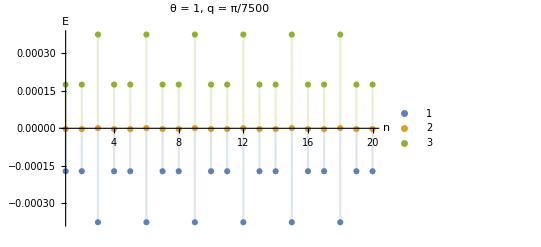

```mathematica
DiscretePlot[{E1, E2, E3},{n, 1, 20}, PlotLegends->Automatic, AxesLabel->{"n", "E"}, PlotLabel->"θ = 1, q = π/7500"]
```

```mathematica
Clear[θ]
n = 12
```

12

```mathematica
Eigs = Eigenvalues[H]
```

{Root[9363922951904296875 π^9-5391349578369140625 √3 π^9+304+#1^3&,1]/(28476562500 (9+16 π^2)^2),Root[1&,2]/(28476562500 (9+1)^2),Root[9363922951904296875 π^9-5391349578369140625 √3 π^9+304+#1^3&,3]/(28476562500 (9+16 π^2)^2)}
 |  |  |  |

```mathematica
E1 = Part[Eigs, 1]
E2 = Part[Eigs, 2]
E3 = Part[Eigs, 3]
```

Root[9363922951904296875 π^9-5391349578369140625 √3 π^9+304+#1^3&,1]/(28476562500 (9+16 π^2)^2)
 |  |  |  |

Root[9363922951904296875 π^9-5391349578369140625 √3 π^9+304+#1^3&,2]/(28476562500 (9+16 π^2)^2)
 |  |  |  |

Root[9363922951904296875 π^9-5391349578369140625 √3 π^9+304+#1^3&,3]/(28476562500 (9+16 π^2)^2)
 |  |  |  |

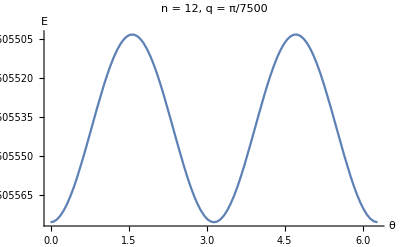

```mathematica
Plot[{E1},{θ, 0, 2 π}, PlotLegends->Automatic, AxesLabel->{"θ", "E"}, PlotLabel->"n = 12, q = π/7500"]
```

```mathematica
Clear[n, θ, q]
```

```mathematica
n = 12
θ = 1
```

12

1

```mathematica
Eigs = Eigenvalues[H]
```

{(π^3 Root[76709256822-44165935746 √3+487+#1^3&,1])/(45562500 (9+16 π^2)^2),(π^3 Root[490+#1^3&,2])/(45562500 (9+16 1)^2),(π^3 Root[76709256822-44165935746 √3+487+#1^3&,3])/(45562500 (9+16 π^2)^2)}
 |  |  |  |

```mathematica
E1 = Part[Eigs, 1]
E2 = Part[Eigs, 2]
E3 = Part[Eigs, 3]
```

1/(45562500 (9+16 π^2)^2)π^3 Root[76709256822-44165935746 √3+694257516288 π^2-400851065952 √3 π^2+595077871104 π^3-330598817280 √3 π^3+2666830459392 π^4-1586874322944 √3 π^4+4584303599616 π^5-2350924922880 √3 π^5+5563855650816 π^6-3656994324480 √3 π^6+14419006193664 π^7-6269133127680 √3 π^7+6617418301440 π^8-5456467722240 √3 π^8+23404763676672 π^9-7430083706880 √3 π^9+4210380767232 π^10-5324893323264 √3 π^10+19813556551680 π^11-3302259425280 √3 π^11+1100753141760 π^12-3082108796928 √3 π^12+7044820107264 π^13-782757789696 √3 π^14-948405357072 ⅈ π q Cos[1]+557885504160 ⅈ √3 π q Cos[1]+2231542016640 ⅈ π^2 q Cos[1]-1338925209984 ⅈ √3 π^2 q Cos[1]-6496266759552 ⅈ π^3 q Cos[1]+3868006162176 ⅈ √3 π^3 q Cos[1]+7140934453248 ⅈ π^4 q Cos[1]-4760622968832 ⅈ √3 π^4 q Cos[1]-19571449982976 ⅈ π^5 q Cos[1]+10579162152960 ⅈ √3 π^5 q Cos[1]-1410554953728 ⅈ π^6 q Cos[1]+2821109907456 ⅈ √3 π^6 q Cos[1]-36360972140544 ⅈ π^7 q Cos[1]+13478636224512 ⅈ √3 π^7 q Cos[1]-17553572757504 ⅈ π^8 q Cos[1]+35107145515008 ⅈ √3 π^8 q Cos[1]-45695014797312 ⅈ π^9 q Cos[1]+6129819058176 ⅈ √3 π^9 q Cos[1]+57954652913664 ⅈ √3 π^10 q Cos[1]-34178385051648 ⅈ π^11 q Cos[1]-1981355655168 ⅈ √3 π^11 q Cos[1]+15850845241344 ⅈ π^12 q Cos[1]+31701690482688 ⅈ √3 π^12 q Cos[1]-10567230160896 ⅈ π^13 q Cos[1]-1761205026816 ⅈ √3 π^13 q Cos[1]+948405357072 ⅈ π Conjugate[q] Cos[1]-557885504160 ⅈ √3 π Conjugate[q] Cos[1]-2231542016640 ⅈ π^2 Conjugate[q] Cos[1]+1338925209984 ⅈ √3 π^2 Conjugate[q] Cos[1]+6496266759552 ⅈ π^3 Conjugate[q] Cos[1]-3868006162176 ⅈ √3 π^3 Conjugate[q] Cos[1]-7140934453248 ⅈ π^4 Conjugate[q] Cos[1]+4760622968832 ⅈ √3 π^4 Conjugate[q] Cos[1]+19571449982976 ⅈ π^5 Conjugate[q] Cos[1]-10579162152960 ⅈ √3 π^5 Conjugate[q] Cos[1]+1410554953728 ⅈ π^6 Conjugate[q] Cos[1]-2821109907456 ⅈ √3 π^6 Conjugate[q] Cos[1]+36360972140544 ⅈ π^7 Conjugate[q] Cos[1]-13478636224512 ⅈ √3 π^7 Conjugate[q] Cos[1]+17553572757504 ⅈ π^8 Conjugate[q] Cos[1]-35107145515008 ⅈ √3 π^8 Conjugate[q] Cos[1]+45695014797312 ⅈ π^9 Conjugate[q] Cos[1]-6129819058176 ⅈ √3 π^9 Conjugate[q] Cos[1]-57954652913664 ⅈ √3 π^10 Conjugate[q] Cos[1]+34178385051648 ⅈ π^11 Conjugate[q] Cos[1]+1981355655168 ⅈ √3 π^11 Conjugate[q] Cos[1]-15850845241344 ⅈ π^12 Conjugate[q] Cos[1]-31701690482688 ⅈ √3 π^12 Conjugate[q] Cos[1]+10567230160896 ⅈ π^13 Conjugate[q] Cos[1]+1761205026816 ⅈ √3 π^13 Conjugate[q] Cos[1]+3347313024960 π^2 q^2 Cos[1]^2-2454696218304 √3 π^2 q^2 Cos[1]^2+74979811759104 π^3 q^2 Cos[1]^2-39275139492864 √3 π^3 q^2 Cos[1]^2+26183426328576 π^4 q^2 Cos[1]^2-23803114844160 √3 π^4 q^2 Cos[1]^2+437977313132544 π^5 q^2 Cos[1]^2-184077421461504 √3 π^5 q^2 Cos[1]^2+88864962084864 π^6 q^2 Cos[1]^2-76169967501312 √3 π^6 q^2 Cos[1]^2+914039610015744 π^7 q^2 Cos[1]^2-304679870005248 √3 π^7 q^2 Cos[1]^2+150459195064320 π^8 q^2 Cos[1]^2-107829089796096 √3 π^8 q^2 Cos[1]^2+782387814334464 π^9 q^2 Cos[1]^2-220673486094336 √3 π^9 q^2 Cos[1]^2+113680280715264 π^10 q^2 Cos[1]^2-73557828698112 √3 π^10 q^2 Cos[1]^2+213986410758144 π^11 q^2 Cos[1]^2-71328803586048 √3 π^11 q^2 Cos[1]^2+23776267862016 π^12 q^2 Cos[1]^2-23776267862016 √3 π^12 q^2 Cos[1]^2+3347313024960 π^2 Conjugate[q]^2 Cos[1]^2-2454696218304 √3 π^2 Conjugate[q]^2 Cos[1]^2+74979811759104 π^3 Conjugate[q]^2 Cos[1]^2-39275139492864 √3 π^3 Conjugate[q]^2 Cos[1]^2+26183426328576 π^4 Conjugate[q]^2 Cos[1]^2-23803114844160 √3 π^4 Conjugate[q]^2 Cos[1]^2+437977313132544 π^5 Conjugate[q]^2 Cos[1]^2-184077421461504 √3 π^5 Conjugate[q]^2 Cos[1]^2+88864962084864 π^6 Conjugate[q]^2 Cos[1]^2-76169967501312 √3 π^6 Conjugate[q]^2 Cos[1]^2+914039610015744 π^7 Conjugate[q]^2 Cos[1]^2-304679870005248 √3 π^7 Conjugate[q]^2 Cos[1]^2+150459195064320 π^8 Conjugate[q]^2 Cos[1]^2-107829089796096 √3 π^8 Conjugate[q]^2 Cos[1]^2+782387814334464 π^9 Conjugate[q]^2 Cos[1]^2-220673486094336 √3 π^9 Conjugate[q]^2 Cos[1]^2+113680280715264 π^10 Conjugate[q]^2 Cos[1]^2-73557828698112 √3 π^10 Conjugate[q]^2 Cos[1]^2+213986410758144 π^11 Conjugate[q]^2 Cos[1]^2-71328803586048 √3 π^11 Conjugate[q]^2 Cos[1]^2+23776267862016 π^12 Conjugate[q]^2 Cos[1]^2-23776267862016 √3 π^12 Conjugate[q]^2 Cos[1]^2-32134205039616 ⅈ π^3 q^3 Cos[1]^3+10711401679872 ⅈ √3 π^3 q^3 Cos[1]^3-171382426877952 ⅈ π^4 q^3 Cos[1]^3+171382426877952 ⅈ √3 π^4 q^3 Cos[1]^3-285637378129920 ⅈ π^5 q^3 Cos[1]^3+19042491875328 ⅈ √3 π^5 q^3 Cos[1]^3+1218719480020992 ⅈ √3 π^6 q^3 Cos[1]^3-914039610015744 ⅈ π^7 q^3 Cos[1]^3-101559956668416 ⅈ √3 π^7 q^3 Cos[1]^3+1624959306694656 ⅈ π^8 q^3 Cos[1]^3+2708265511157760 ⅈ √3 π^8 q^3 Cos[1]^3-1263857238540288 ⅈ π^9 q^3 Cos[1]^3-300918390128640 ⅈ √3 π^9 q^3 Cos[1]^3+1925877696823296 ⅈ π^10 q^3 Cos[1]^3+1925877696823296 ⅈ √3 π^10 q^3 Cos[1]^3-641959232274432 ⅈ π^11 q^3 Cos[1]^3-213986410758144 ⅈ √3 π^11 q^3 Cos[1]^3+32134205039616 ⅈ π^3 Conjugate[q]^3 Cos[1]^3-10711401679872 ⅈ √3 π^3 Conjugate[q]^3 Cos[1]^3+171382426877952 ⅈ π^4 Conjugate[q]^3 Cos[1]^3-171382426877952 ⅈ √3 π^4 Conjugate[q]^3 Cos[1]^3+285637378129920 ⅈ π^5 Conjugate[q]^3 Cos[1]^3-19042491875328 ⅈ √3 π^5 Conjugate[q]^3 Cos[1]^3-1218719480020992 ⅈ √3 π^6 Conjugate[q]^3 Cos[1]^3+914039610015744 ⅈ π^7 Conjugate[q]^3 Cos[1]^3+101559956668416 ⅈ √3 π^7 Conjugate[q]^3 Cos[1]^3-1624959306694656 ⅈ π^8 Conjugate[q]^3 Cos[1]^3-2708265511157760 ⅈ √3 π^8 Conjugate[q]^3 Cos[1]^3+1263857238540288 ⅈ π^9 Conjugate[q]^3 Cos[1]^3+300918390128640 ⅈ √3 π^9 Conjugate[q]^3 Cos[1]^3-1925877696823296 ⅈ π^10 Conjugate[q]^3 Cos[1]^3-1925877696823296 ⅈ √3 π^10 Conjugate[q]^3 Cos[1]^3+641959232274432 ⅈ π^11 Conjugate[q]^3 Cos[1]^3+213986410758144 ⅈ √3 π^11 Conjugate[q]^3 Cos[1]^3-669462604992 ⅈ π q Sin[1]+390519852912 ⅈ √3 π q Sin[1]-4016775629952 ⅈ π^2 q Sin[1]+2231542016640 ⅈ √3 π^2 q Sin[1]-5653239775488 ⅈ π^3 q Sin[1]+3520877404032 ⅈ √3 π^3 q Sin[1]-33324360781824 ⅈ π^4 q Sin[1]+16662180390912 ⅈ √3 π^4 q Sin[1]-17984575660032 ⅈ π^5 q Sin[1]+14281868906496 ⅈ √3 π^5 q Sin[1]-118486616113152 ⅈ π^6 q Sin[1]+43727203565568 ⅈ √3 π^6 q Sin[1]-25389989167104 ⅈ π^7 q Sin[1]+33226405576704 ⅈ √3 π^7 q Sin[1]-225688792596480 ⅈ π^8 q Sin[1]+42630105268224 ⅈ √3 π^8 q Sin[1]-11702381838336 ⅈ π^9 q Sin[1]+45695014797312 ⅈ √3 π^9 q Sin[1]-227360561430528 ⅈ π^10 q Sin[1]+5944066965504 ⅈ π^11 q Sin[1]+34178385051648 ⅈ √3 π^11 q Sin[1]-95105071448064 ⅈ π^12 q Sin[1]-15850845241344 ⅈ √3 π^12 q Sin[1]+5283615080448 ⅈ π^13 q Sin[1]+10567230160896 ⅈ √3 π^13 q Sin[1]+669462604992 ⅈ π Conjugate[q] Sin[1]-390519852912 ⅈ √3 π Conjugate[q] Sin[1]+4016775629952 ⅈ π^2 Conjugate[q] Sin[1]-2231542016640 ⅈ √3 π^2 Conjugate[q] Sin[1]+5653239775488 ⅈ π^3 Conjugate[q] Sin[1]-3520877404032 ⅈ √3 π^3 Conjugate[q] Sin[1]+33324360781824 ⅈ π^4 Conjugate[q] Sin[1]-16662180390912 ⅈ √3 π^4 Conjugate[q] Sin[1]+17984575660032 ⅈ π^5 Conjugate[q] Sin[1]-14281868906496 ⅈ √3 π^5 Conjugate[q] Sin[1]+118486616113152 ⅈ π^6 Conjugate[q] Sin[1]-43727203565568 ⅈ √3 π^6 Conjugate[q] Sin[1]+25389989167104 ⅈ π^7 Conjugate[q] Sin[1]-33226405576704 ⅈ √3 π^7 Conjugate[q] Sin[1]+225688792596480 ⅈ π^8 Conjugate[q] Sin[1]-42630105268224 ⅈ √3 π^8 Conjugate[q] Sin[1]+11702381838336 ⅈ π^9 Conjugate[q] Sin[1]-45695014797312 ⅈ √3 π^9 Conjugate[q] Sin[1]+227360561430528 ⅈ π^10 Conjugate[q] Sin[1]-5944066965504 ⅈ π^11 Conjugate[q] Sin[1]-34178385051648 ⅈ √3 π^11 Conjugate[q] Sin[1]+95105071448064 ⅈ π^12 Conjugate[q] Sin[1]+15850845241344 ⅈ √3 π^12 Conjugate[q] Sin[1]-5283615080448 ⅈ π^13 Conjugate[q] Sin[1]-10567230160896 ⅈ √3 π^13 Conjugate[q] Sin[1]-18744952939776 π^2 q^2 Cos[1] Sin[1]+10711401679872 √3 π^2 q^2 Cos[1] Sin[1]-107114016798720 π^3 q^2 Cos[1] Sin[1]+64268410079232 √3 π^3 q^2 Cos[1] Sin[1]-135677754611712 π^4 q^2 Cos[1] Sin[1]+71409344532480 √3 π^4 q^2 Cos[1] Sin[1]-609359740010496 π^5 q^2 Cos[1] Sin[1]+418934821257216 √3 π^5 q^2 Cos[1] Sin[1]-444324810424320 π^6 q^2 Cos[1] Sin[1]+160803264724992 √3 π^6 q^2 Cos[1] Sin[1]-1015599566684160 π^7 q^2 Cos[1] Sin[1]+1151012842242048 √3 π^7 q^2 Cos[1] Sin[1]-804956693594112 π^8 q^2 Cos[1] Sin[1]+120367356051456 √3 π^8 q^2 Cos[1] Sin[1]-240734712102912 π^9 q^2 Cos[1] Sin[1]+1564775628668928 √3 π^9 q^2 Cos[1] Sin[1]-762326588325888 π^10 q^2 Cos[1] Sin[1]-26748301344768 √3 π^10 q^2 Cos[1] Sin[1]+427972821516288 π^11 q^2 Cos[1] Sin[1]+855945643032576 √3 π^11 q^2 Cos[1] Sin[1]-285315214344192 π^12 q^2 Cos[1] Sin[1]-47552535724032 √3 π^12 q^2 Cos[1] Sin[1]-18744952939776 π^2 Conjugate[q]^2 Cos[1] Sin[1]+10711401679872 √3 π^2 Conjugate[q]^2 Cos[1] Sin[1]-107114016798720 π^3 Conjugate[q]^2 Cos[1] Sin[1]+64268410079232 √3 π^3 Conjugate[q]^2 Cos[1] Sin[1]-135677754611712 π^4 Conjugate[q]^2 Cos[1] Sin[1]+71409344532480 √3 π^4 Conjugate[q]^2 Cos[1] Sin[1]-609359740010496 π^5 Conjugate[q]^2 Cos[1] Sin[1]+418934821257216 √3 π^5 Conjugate[q]^2 Cos[1] Sin[1]-444324810424320 π^6 Conjugate[q]^2 Cos[1] Sin[1]+160803264724992 √3 π^6 Conjugate[q]^2 Cos[1] Sin[1]-1015599566684160 π^7 Conjugate[q]^2 Cos[1] Sin[1]+1151012842242048 √3 π^7 Conjugate[q]^2 Cos[1] Sin[1]-804956693594112 π^8 Conjugate[q]^2 Cos[1] Sin[1]+120367356051456 √3 π^8 Conjugate[q]^2 Cos[1] Sin[1]-240734712102912 π^9 Conjugate[q]^2 Cos[1] Sin[1]+1564775628668928 √3 π^9 Conjugate[q]^2 Cos[1] Sin[1]-762326588325888 π^10 Conjugate[q]^2 Cos[1] Sin[1]-26748301344768 √3 π^10 Conjugate[q]^2 Cos[1] Sin[1]+427972821516288 π^11 Conjugate[q]^2 Cos[1] Sin[1]+855945643032576 √3 π^11 Conjugate[q]^2 Cos[1] Sin[1]-285315214344192 π^12 Conjugate[q]^2 Cos[1] Sin[1]-47552535724032 √3 π^12 Conjugate[q]^2 Cos[1] Sin[1]-2008387814976 π^2 q^2 Sin[1]^2+2008387814976 √3 π^2 q^2 Sin[1]^2-32134205039616 π^3 q^2 Sin[1]^2+10711401679872 √3 π^3 q^2 Sin[1]^2-7140934453248 π^4 q^2 Sin[1]^2+21422803359744 √3 π^4 q^2 Sin[1]^2-285637378129920 π^5 q^2 Sin[1]^2+19042491875328 √3 π^5 q^2 Sin[1]^2+12694994583552 π^6 q^2 Sin[1]^2+88864962084864 √3 π^6 q^2 Sin[1]^2-914039610015744 π^7 q^2 Sin[1]^2-101559956668416 √3 π^7 q^2 Sin[1]^2+90275517038592 π^8 q^2 Sin[1]^2+180551034077184 √3 π^8 q^2 Sin[1]^2-1263857238540288 π^9 q^2 Sin[1]^2-300918390128640 √3 π^9 q^2 Sin[1]^2+140428582060032 π^10 q^2 Sin[1]^2+180551034077184 √3 π^10 q^2 Sin[1]^2-641959232274432 π^11 q^2 Sin[1]^2-213986410758144 √3 π^11 q^2 Sin[1]^2+71328803586048 π^12 q^2 Sin[1]^2+71328803586048 √3 π^12 q^2 Sin[1]^2-2008387814976 π^2 Conjugate[q]^2 Sin[1]^2+2008387814976 √3 π^2 Conjugate[q]^2 Sin[1]^2-32134205039616 π^3 Conjugate[q]^2 Sin[1]^2+10711401679872 √3 π^3 Conjugate[q]^2 Sin[1]^2-7140934453248 π^4 Conjugate[q]^2 Sin[1]^2+21422803359744 √3 π^4 Conjugate[q]^2 Sin[1]^2-285637378129920 π^5 Conjugate[q]^2 Sin[1]^2+19042491875328 √3 π^5 Conjugate[q]^2 Sin[1]^2+12694994583552 π^6 Conjugate[q]^2 Sin[1]^2+88864962084864 √3 π^6 Conjugate[q]^2 Sin[1]^2-914039610015744 π^7 Conjugate[q]^2 Sin[1]^2-101559956668416 √3 π^7 Conjugate[q]^2 Sin[1]^2+90275517038592 π^8 Conjugate[q]^2 Sin[1]^2+180551034077184 √3 π^8 Conjugate[q]^2 Sin[1]^2-1263857238540288 π^9 Conjugate[q]^2 Sin[1]^2-300918390128640 √3 π^9 Conjugate[q]^2 Sin[1]^2+140428582060032 π^10 Conjugate[q]^2 Sin[1]^2+180551034077184 √3 π^10 Conjugate[q]^2 Sin[1]^2-641959232274432 π^11 Conjugate[q]^2 Sin[1]^2-213986410758144 √3 π^11 Conjugate[q]^2 Sin[1]^2+71328803586048 π^12 Conjugate[q]^2 Sin[1]^2+71328803586048 √3 π^12 Conjugate[q]^2 Sin[1]^2+96402615118848 ⅈ π^3 q^3 Cos[1] Sin[1]^2-32134205039616 ⅈ √3 π^3 q^3 Cos[1] Sin[1]^2+514147280633856 ⅈ π^4 q^3 Cos[1] Sin[1]^2-514147280633856 ⅈ √3 π^4 q^3 Cos[1] Sin[1]^2+856912134389760 ⅈ π^5 q^3 Cos[1] Sin[1]^2-57127475625984 ⅈ √3 π^5 q^3 Cos[1] Sin[1]^2-3656158440062976 ⅈ √3 π^6 q^3 Cos[1] Sin[1]^2+2742118830047232 ⅈ π^7 q^3 Cos[1] Sin[1]^2+304679870005248 ⅈ √3 π^7 q^3 Cos[1] Sin[1]^2-4874877920083968 ⅈ π^8 q^3 Cos[1] Sin[1]^2-8124796533473280 ⅈ √3 π^8 q^3 Cos[1] Sin[1]^2+3791571715620864 ⅈ π^9 q^3 Cos[1] Sin[1]^2+902755170385920 ⅈ √3 π^9 q^3 Cos[1] Sin[1]^2-5777633090469888 ⅈ π^10 q^3 Cos[1] Sin[1]^2-5777633090469888 ⅈ √3 π^10 q^3 Cos[1] Sin[1]^2+1925877696823296 ⅈ π^11 q^3 Cos[1] Sin[1]^2+641959232274432 ⅈ √3 π^11 q^3 Cos[1] Sin[1]^2-96402615118848 ⅈ π^3 Conjugate[q]^3 Cos[1] Sin[1]^2+32134205039616 ⅈ √3 π^3 Conjugate[q]^3 Cos[1] Sin[1]^2-514147280633856 ⅈ π^4 Conjugate[q]^3 Cos[1] Sin[1]^2+514147280633856 ⅈ √3 π^4 Conjugate[q]^3 Cos[1] Sin[1]^2-856912134389760 ⅈ π^5 Conjugate[q]^3 Cos[1] Sin[1]^2+57127475625984 ⅈ √3 π^5 Conjugate[q]^3 Cos[1] Sin[1]^2+3656158440062976 ⅈ √3 π^6 Conjugate[q]^3 Cos[1] Sin[1]^2-2742118830047232 ⅈ π^7 Conjugate[q]^3 Cos[1] Sin[1]^2-304679870005248 ⅈ √3 π^7 Conjugate[q]^3 Cos[1] Sin[1]^2+4874877920083968 ⅈ π^8 Conjugate[q]^3 Cos[1] Sin[1]^2+8124796533473280 ⅈ √3 π^8 Conjugate[q]^3 Cos[1] Sin[1]^2-3791571715620864 ⅈ π^9 Conjugate[q]^3 Cos[1] Sin[1]^2-902755170385920 ⅈ √3 π^9 Conjugate[q]^3 Cos[1] Sin[1]^2+5777633090469888 ⅈ π^10 Conjugate[q]^3 Cos[1] Sin[1]^2+5777633090469888 ⅈ √3 π^10 Conjugate[q]^3 Cos[1] Sin[1]^2-1925877696823296 ⅈ π^11 Conjugate[q]^3 Cos[1] Sin[1]^2-641959232274432 ⅈ √3 π^11 Conjugate[q]^3 Cos[1] Sin[1]^2+(-28697814+15943230 √3-175729824 π^2+96367968 √3 π^2-181398528 π^3+90699264 √3 π^3-579467520 π^4+251942400 √3 π^4+322486272 √3 π^5-2329067520 π^6+376233984 √3 π^6+286654464 √3 π^7-1098842112 π^8+318504960 √3 π^8-679477248 π^10+113246208 √3 π^10-201326592 π^12+229582512 ⅈ π q Cos[1]-165809592 ⅈ √3 π q Cos[1]-612220032 ⅈ π^2 q Cos[1]+408146688 ⅈ √3 π^2 q Cos[1]+1972708992 ⅈ π^3 q Cos[1]-1269789696 ⅈ √3 π^3 q Cos[1]-3265173504 ⅈ π^4 q Cos[1]+5562888192 ⅈ π^5 q Cos[1]+1894606848 ⅈ √3 π^5 q Cos[1]-3869835264 ⅈ π^6 q Cos[1]+6664716288 ⅈ π^7 q Cos[1]-6163070976 ⅈ √3 π^7 q Cos[1]+3057647616 ⅈ π^9 q Cos[1]-5096079360 ⅈ √3 π^9 q Cos[1]-1811939328 ⅈ √3 π^11 q Cos[1]-229582512 ⅈ π Conjugate[q] Cos[1]+165809592 ⅈ √3 π Conjugate[q] Cos[1]+612220032 ⅈ π^2 Conjugate[q] Cos[1]-408146688 ⅈ √3 π^2 Conjugate[q] Cos[1]-1972708992 ⅈ π^3 Conjugate[q] Cos[1]+1269789696 ⅈ √3 π^3 Conjugate[q] Cos[1]+3265173504 ⅈ π^4 Conjugate[q] Cos[1]-5562888192 ⅈ π^5 Conjugate[q] Cos[1]-1894606848 ⅈ √3 π^5 Conjugate[q] Cos[1]+3869835264 ⅈ π^6 Conjugate[q] Cos[1]-6664716288 ⅈ π^7 Conjugate[q] Cos[1]+6163070976 ⅈ √3 π^7 Conjugate[q] Cos[1]-3057647616 ⅈ π^9 Conjugate[q] Cos[1]+5096079360 ⅈ √3 π^9 Conjugate[q] Cos[1]+1811939328 ⅈ √3 π^11 Conjugate[q] Cos[1]-10713850560 π^2 q Conjugate[q] Cos[1]^2+4285540224 √3 π^2 q Conjugate[q] Cos[1]^2+9795520512 √3 π^3 q Conjugate[q] Cos[1]^2-133872113664 π^4 q Conjugate[q] Cos[1]^2+23944605696 √3 π^4 q Conjugate[q] Cos[1]^2+17414258688 √3 π^5 q Conjugate[q] Cos[1]^2-111257763840 π^6 q Conjugate[q] Cos[1]^2+44503105536 √3 π^6 q Conjugate[q] Cos[1]^2-110075314176 π^8 q Conjugate[q] Cos[1]^2+27518828544 √3 π^8 q Conjugate[q] Cos[1]^2-48922361856 π^10 q Conjugate[q] Cos[1]^2+191318760 ⅈ π q Sin[1]-76527504 ⅈ √3 π q Sin[1]+1224440064 ⅈ π^2 q Sin[1]-612220032 ⅈ √3 π^2 q Sin[1]+1088391168 ⅈ π^3 q Sin[1]-68024448 ⅈ √3 π^3 q Sin[1]-3265173504 ⅈ √3 π^4 q Sin[1]+19470108672 ⅈ π^5 q Sin[1]+241864704 ⅈ √3 π^5 q Sin[1]-3869835264 ⅈ √3 π^6 q Sin[1]+1289945088 ⅈ π^7 q Sin[1]+214990848 ⅈ √3 π^7 q Sin[1]-191318760 ⅈ π Conjugate[q] Sin[1]+76527504 ⅈ √3 π Conjugate[q] Sin[1]-1224440064 ⅈ π^2 Conjugate[q] Sin[1]+612220032 ⅈ √3 π^2 Conjugate[q] Sin[1]-1088391168 ⅈ π^3 Conjugate[q] Sin[1]+68024448 ⅈ √3 π^3 Conjugate[q] Sin[1]+3265173504 ⅈ √3 π^4 Conjugate[q] Sin[1]-19470108672 ⅈ π^5 Conjugate[q] Sin[1]-241864704 ⅈ √3 π^5 Conjugate[q] Sin[1]+3869835264 ⅈ √3 π^6 Conjugate[q] Sin[1]-1289945088 ⅈ π^7 Conjugate[q] Sin[1]-214990848 ⅈ √3 π^7 Conjugate[q] Sin[1]+3673320192 π^2 q Conjugate[q] Cos[1] Sin[1]+612220032 √3 π^2 q Conjugate[q] Cos[1] Sin[1]+58773123072 π^3 q Conjugate[q] Cos[1] Sin[1]+13060694016 π^4 q Conjugate[q] Cos[1] Sin[1]-154551545856 √3 π^4 q Conjugate[q] Cos[1] Sin[1]+104485552128 π^5 q Conjugate[q] Cos[1] Sin[1]+11609505792 π^6 q Conjugate[q] Cos[1] Sin[1]+1934917632 √3 π^6 q Conjugate[q] Cos[1] Sin[1]-6428310336 π^2 q Conjugate[q] Sin[1]^2-1836660096 √3 π^2 q Conjugate[q] Sin[1]^2+29386561536 √3 π^3 q Conjugate[q] Sin[1]^2-257948706816 π^4 q Conjugate[q] Sin[1]^2-6530347008 √3 π^4 q Conjugate[q] Sin[1]^2+52242776064 √3 π^5 q Conjugate[q] Sin[1]^2-20316635136 π^6 q Conjugate[q] Sin[1]^2-5804752896 √3 π^6 q Conjugate[q] Sin[1]^2) #1+#1^3&,1]

1/(45562500 (9+16 π^2)^2)π^3 Root[76709256822-44165935746 √3+694257516288 π^2-400851065952 √3 π^2+595077871104 π^3-330598817280 √3 π^3+2666830459392 π^4-1586874322944 √3 π^4+4584303599616 π^5-2350924922880 √3 π^5+5563855650816 π^6-3656994324480 √3 π^6+14419006193664 π^7-6269133127680 √3 π^7+6617418301440 π^8-5456467722240 √3 π^8+23404763676672 π^9-7430083706880 √3 π^9+4210380767232 π^10-5324893323264 √3 π^10+19813556551680 π^11-3302259425280 √3 π^11+1100753141760 π^12-3082108796928 √3 π^12+7044820107264 π^13-782757789696 √3 π^14-948405357072 ⅈ π q Cos[1]+557885504160 ⅈ √3 π q Cos[1]+2231542016640 ⅈ π^2 q Cos[1]-1338925209984 ⅈ √3 π^2 q Cos[1]-6496266759552 ⅈ π^3 q Cos[1]+3868006162176 ⅈ √3 π^3 q Cos[1]+7140934453248 ⅈ π^4 q Cos[1]-4760622968832 ⅈ √3 π^4 q Cos[1]-19571449982976 ⅈ π^5 q Cos[1]+10579162152960 ⅈ √3 π^5 q Cos[1]-1410554953728 ⅈ π^6 q Cos[1]+2821109907456 ⅈ √3 π^6 q Cos[1]-36360972140544 ⅈ π^7 q Cos[1]+13478636224512 ⅈ √3 π^7 q Cos[1]-17553572757504 ⅈ π^8 q Cos[1]+35107145515008 ⅈ √3 π^8 q Cos[1]-45695014797312 ⅈ π^9 q Cos[1]+6129819058176 ⅈ √3 π^9 q Cos[1]+57954652913664 ⅈ √3 π^10 q Cos[1]-34178385051648 ⅈ π^11 q Cos[1]-1981355655168 ⅈ √3 π^11 q Cos[1]+15850845241344 ⅈ π^12 q Cos[1]+31701690482688 ⅈ √3 π^12 q Cos[1]-10567230160896 ⅈ π^13 q Cos[1]-1761205026816 ⅈ √3 π^13 q Cos[1]+948405357072 ⅈ π Conjugate[q] Cos[1]-557885504160 ⅈ √3 π Conjugate[q] Cos[1]-2231542016640 ⅈ π^2 Conjugate[q] Cos[1]+1338925209984 ⅈ √3 π^2 Conjugate[q] Cos[1]+6496266759552 ⅈ π^3 Conjugate[q] Cos[1]-3868006162176 ⅈ √3 π^3 Conjugate[q] Cos[1]-7140934453248 ⅈ π^4 Conjugate[q] Cos[1]+4760622968832 ⅈ √3 π^4 Conjugate[q] Cos[1]+19571449982976 ⅈ π^5 Conjugate[q] Cos[1]-10579162152960 ⅈ √3 π^5 Conjugate[q] Cos[1]+1410554953728 ⅈ π^6 Conjugate[q] Cos[1]-2821109907456 ⅈ √3 π^6 Conjugate[q] Cos[1]+36360972140544 ⅈ π^7 Conjugate[q] Cos[1]-13478636224512 ⅈ √3 π^7 Conjugate[q] Cos[1]+17553572757504 ⅈ π^8 Conjugate[q] Cos[1]-35107145515008 ⅈ √3 π^8 Conjugate[q] Cos[1]+45695014797312 ⅈ π^9 Conjugate[q] Cos[1]-6129819058176 ⅈ √3 π^9 Conjugate[q] Cos[1]-57954652913664 ⅈ √3 π^10 Conjugate[q] Cos[1]+34178385051648 ⅈ π^11 Conjugate[q] Cos[1]+1981355655168 ⅈ √3 π^11 Conjugate[q] Cos[1]-15850845241344 ⅈ π^12 Conjugate[q] Cos[1]-31701690482688 ⅈ √3 π^12 Conjugate[q] Cos[1]+10567230160896 ⅈ π^13 Conjugate[q] Cos[1]+1761205026816 ⅈ √3 π^13 Conjugate[q] Cos[1]+3347313024960 π^2 q^2 Cos[1]^2-2454696218304 √3 π^2 q^2 Cos[1]^2+74979811759104 π^3 q^2 Cos[1]^2-39275139492864 √3 π^3 q^2 Cos[1]^2+26183426328576 π^4 q^2 Cos[1]^2-23803114844160 √3 π^4 q^2 Cos[1]^2+437977313132544 π^5 q^2 Cos[1]^2-184077421461504 √3 π^5 q^2 Cos[1]^2+88864962084864 π^6 q^2 Cos[1]^2-76169967501312 √3 π^6 q^2 Cos[1]^2+914039610015744 π^7 q^2 Cos[1]^2-304679870005248 √3 π^7 q^2 Cos[1]^2+150459195064320 π^8 q^2 Cos[1]^2-107829089796096 √3 π^8 q^2 Cos[1]^2+782387814334464 π^9 q^2 Cos[1]^2-220673486094336 √3 π^9 q^2 Cos[1]^2+113680280715264 π^10 q^2 Cos[1]^2-73557828698112 √3 π^10 q^2 Cos[1]^2+213986410758144 π^11 q^2 Cos[1]^2-71328803586048 √3 π^11 q^2 Cos[1]^2+23776267862016 π^12 q^2 Cos[1]^2-23776267862016 √3 π^12 q^2 Cos[1]^2+3347313024960 π^2 Conjugate[q]^2 Cos[1]^2-2454696218304 √3 π^2 Conjugate[q]^2 Cos[1]^2+74979811759104 π^3 Conjugate[q]^2 Cos[1]^2-39275139492864 √3 π^3 Conjugate[q]^2 Cos[1]^2+26183426328576 π^4 Conjugate[q]^2 Cos[1]^2-23803114844160 √3 π^4 Conjugate[q]^2 Cos[1]^2+437977313132544 π^5 Conjugate[q]^2 Cos[1]^2-184077421461504 √3 π^5 Conjugate[q]^2 Cos[1]^2+88864962084864 π^6 Conjugate[q]^2 Cos[1]^2-76169967501312 √3 π^6 Conjugate[q]^2 Cos[1]^2+914039610015744 π^7 Conjugate[q]^2 Cos[1]^2-304679870005248 √3 π^7 Conjugate[q]^2 Cos[1]^2+150459195064320 π^8 Conjugate[q]^2 Cos[1]^2-107829089796096 √3 π^8 Conjugate[q]^2 Cos[1]^2+782387814334464 π^9 Conjugate[q]^2 Cos[1]^2-220673486094336 √3 π^9 Conjugate[q]^2 Cos[1]^2+113680280715264 π^10 Conjugate[q]^2 Cos[1]^2-73557828698112 √3 π^10 Conjugate[q]^2 Cos[1]^2+213986410758144 π^11 Conjugate[q]^2 Cos[1]^2-71328803586048 √3 π^11 Conjugate[q]^2 Cos[1]^2+23776267862016 π^12 Conjugate[q]^2 Cos[1]^2-23776267862016 √3 π^12 Conjugate[q]^2 Cos[1]^2-32134205039616 ⅈ π^3 q^3 Cos[1]^3+10711401679872 ⅈ √3 π^3 q^3 Cos[1]^3-171382426877952 ⅈ π^4 q^3 Cos[1]^3+171382426877952 ⅈ √3 π^4 q^3 Cos[1]^3-285637378129920 ⅈ π^5 q^3 Cos[1]^3+19042491875328 ⅈ √3 π^5 q^3 Cos[1]^3+1218719480020992 ⅈ √3 π^6 q^3 Cos[1]^3-914039610015744 ⅈ π^7 q^3 Cos[1]^3-101559956668416 ⅈ √3 π^7 q^3 Cos[1]^3+1624959306694656 ⅈ π^8 q^3 Cos[1]^3+2708265511157760 ⅈ √3 π^8 q^3 Cos[1]^3-1263857238540288 ⅈ π^9 q^3 Cos[1]^3-300918390128640 ⅈ √3 π^9 q^3 Cos[1]^3+1925877696823296 ⅈ π^10 q^3 Cos[1]^3+1925877696823296 ⅈ √3 π^10 q^3 Cos[1]^3-641959232274432 ⅈ π^11 q^3 Cos[1]^3-213986410758144 ⅈ √3 π^11 q^3 Cos[1]^3+32134205039616 ⅈ π^3 Conjugate[q]^3 Cos[1]^3-10711401679872 ⅈ √3 π^3 Conjugate[q]^3 Cos[1]^3+171382426877952 ⅈ π^4 Conjugate[q]^3 Cos[1]^3-171382426877952 ⅈ √3 π^4 Conjugate[q]^3 Cos[1]^3+285637378129920 ⅈ π^5 Conjugate[q]^3 Cos[1]^3-19042491875328 ⅈ √3 π^5 Conjugate[q]^3 Cos[1]^3-1218719480020992 ⅈ √3 π^6 Conjugate[q]^3 Cos[1]^3+914039610015744 ⅈ π^7 Conjugate[q]^3 Cos[1]^3+101559956668416 ⅈ √3 π^7 Conjugate[q]^3 Cos[1]^3-1624959306694656 ⅈ π^8 Conjugate[q]^3 Cos[1]^3-2708265511157760 ⅈ √3 π^8 Conjugate[q]^3 Cos[1]^3+1263857238540288 ⅈ π^9 Conjugate[q]^3 Cos[1]^3+300918390128640 ⅈ √3 π^9 Conjugate[q]^3 Cos[1]^3-1925877696823296 ⅈ π^10 Conjugate[q]^3 Cos[1]^3-1925877696823296 ⅈ √3 π^10 Conjugate[q]^3 Cos[1]^3+641959232274432 ⅈ π^11 Conjugate[q]^3 Cos[1]^3+213986410758144 ⅈ √3 π^11 Conjugate[q]^3 Cos[1]^3-669462604992 ⅈ π q Sin[1]+390519852912 ⅈ √3 π q Sin[1]-4016775629952 ⅈ π^2 q Sin[1]+2231542016640 ⅈ √3 π^2 q Sin[1]-5653239775488 ⅈ π^3 q Sin[1]+3520877404032 ⅈ √3 π^3 q Sin[1]-33324360781824 ⅈ π^4 q Sin[1]+16662180390912 ⅈ √3 π^4 q Sin[1]-17984575660032 ⅈ π^5 q Sin[1]+14281868906496 ⅈ √3 π^5 q Sin[1]-118486616113152 ⅈ π^6 q Sin[1]+43727203565568 ⅈ √3 π^6 q Sin[1]-25389989167104 ⅈ π^7 q Sin[1]+33226405576704 ⅈ √3 π^7 q Sin[1]-225688792596480 ⅈ π^8 q Sin[1]+42630105268224 ⅈ √3 π^8 q Sin[1]-11702381838336 ⅈ π^9 q Sin[1]+45695014797312 ⅈ √3 π^9 q Sin[1]-227360561430528 ⅈ π^10 q Sin[1]+5944066965504 ⅈ π^11 q Sin[1]+34178385051648 ⅈ √3 π^11 q Sin[1]-95105071448064 ⅈ π^12 q Sin[1]-15850845241344 ⅈ √3 π^12 q Sin[1]+5283615080448 ⅈ π^13 q Sin[1]+10567230160896 ⅈ √3 π^13 q Sin[1]+669462604992 ⅈ π Conjugate[q] Sin[1]-390519852912 ⅈ √3 π Conjugate[q] Sin[1]+4016775629952 ⅈ π^2 Conjugate[q] Sin[1]-2231542016640 ⅈ √3 π^2 Conjugate[q] Sin[1]+5653239775488 ⅈ π^3 Conjugate[q] Sin[1]-3520877404032 ⅈ √3 π^3 Conjugate[q] Sin[1]+33324360781824 ⅈ π^4 Conjugate[q] Sin[1]-16662180390912 ⅈ √3 π^4 Conjugate[q] Sin[1]+17984575660032 ⅈ π^5 Conjugate[q] Sin[1]-14281868906496 ⅈ √3 π^5 Conjugate[q] Sin[1]+118486616113152 ⅈ π^6 Conjugate[q] Sin[1]-43727203565568 ⅈ √3 π^6 Conjugate[q] Sin[1]+25389989167104 ⅈ π^7 Conjugate[q] Sin[1]-33226405576704 ⅈ √3 π^7 Conjugate[q] Sin[1]+225688792596480 ⅈ π^8 Conjugate[q] Sin[1]-42630105268224 ⅈ √3 π^8 Conjugate[q] Sin[1]+11702381838336 ⅈ π^9 Conjugate[q] Sin[1]-45695014797312 ⅈ √3 π^9 Conjugate[q] Sin[1]+227360561430528 ⅈ π^10 Conjugate[q] Sin[1]-5944066965504 ⅈ π^11 Conjugate[q] Sin[1]-34178385051648 ⅈ √3 π^11 Conjugate[q] Sin[1]+95105071448064 ⅈ π^12 Conjugate[q] Sin[1]+15850845241344 ⅈ √3 π^12 Conjugate[q] Sin[1]-5283615080448 ⅈ π^13 Conjugate[q] Sin[1]-10567230160896 ⅈ √3 π^13 Conjugate[q] Sin[1]-18744952939776 π^2 q^2 Cos[1] Sin[1]+10711401679872 √3 π^2 q^2 Cos[1] Sin[1]-107114016798720 π^3 q^2 Cos[1] Sin[1]+64268410079232 √3 π^3 q^2 Cos[1] Sin[1]-135677754611712 π^4 q^2 Cos[1] Sin[1]+71409344532480 √3 π^4 q^2 Cos[1] Sin[1]-609359740010496 π^5 q^2 Cos[1] Sin[1]+418934821257216 √3 π^5 q^2 Cos[1] Sin[1]-444324810424320 π^6 q^2 Cos[1] Sin[1]+160803264724992 √3 π^6 q^2 Cos[1] Sin[1]-1015599566684160 π^7 q^2 Cos[1] Sin[1]+1151012842242048 √3 π^7 q^2 Cos[1] Sin[1]-804956693594112 π^8 q^2 Cos[1] Sin[1]+120367356051456 √3 π^8 q^2 Cos[1] Sin[1]-240734712102912 π^9 q^2 Cos[1] Sin[1]+1564775628668928 √3 π^9 q^2 Cos[1] Sin[1]-762326588325888 π^10 q^2 Cos[1] Sin[1]-26748301344768 √3 π^10 q^2 Cos[1] Sin[1]+427972821516288 π^11 q^2 Cos[1] Sin[1]+855945643032576 √3 π^11 q^2 Cos[1] Sin[1]-285315214344192 π^12 q^2 Cos[1] Sin[1]-47552535724032 √3 π^12 q^2 Cos[1] Sin[1]-18744952939776 π^2 Conjugate[q]^2 Cos[1] Sin[1]+10711401679872 √3 π^2 Conjugate[q]^2 Cos[1] Sin[1]-107114016798720 π^3 Conjugate[q]^2 Cos[1] Sin[1]+64268410079232 √3 π^3 Conjugate[q]^2 Cos[1] Sin[1]-135677754611712 π^4 Conjugate[q]^2 Cos[1] Sin[1]+71409344532480 √3 π^4 Conjugate[q]^2 Cos[1] Sin[1]-609359740010496 π^5 Conjugate[q]^2 Cos[1] Sin[1]+418934821257216 √3 π^5 Conjugate[q]^2 Cos[1] Sin[1]-444324810424320 π^6 Conjugate[q]^2 Cos[1] Sin[1]+160803264724992 √3 π^6 Conjugate[q]^2 Cos[1] Sin[1]-1015599566684160 π^7 Conjugate[q]^2 Cos[1] Sin[1]+1151012842242048 √3 π^7 Conjugate[q]^2 Cos[1] Sin[1]-804956693594112 π^8 Conjugate[q]^2 Cos[1] Sin[1]+120367356051456 √3 π^8 Conjugate[q]^2 Cos[1] Sin[1]-240734712102912 π^9 Conjugate[q]^2 Cos[1] Sin[1]+1564775628668928 √3 π^9 Conjugate[q]^2 Cos[1] Sin[1]-762326588325888 π^10 Conjugate[q]^2 Cos[1] Sin[1]-26748301344768 √3 π^10 Conjugate[q]^2 Cos[1] Sin[1]+427972821516288 π^11 Conjugate[q]^2 Cos[1] Sin[1]+855945643032576 √3 π^11 Conjugate[q]^2 Cos[1] Sin[1]-285315214344192 π^12 Conjugate[q]^2 Cos[1] Sin[1]-47552535724032 √3 π^12 Conjugate[q]^2 Cos[1] Sin[1]-2008387814976 π^2 q^2 Sin[1]^2+2008387814976 √3 π^2 q^2 Sin[1]^2-32134205039616 π^3 q^2 Sin[1]^2+10711401679872 √3 π^3 q^2 Sin[1]^2-7140934453248 π^4 q^2 Sin[1]^2+21422803359744 √3 π^4 q^2 Sin[1]^2-285637378129920 π^5 q^2 Sin[1]^2+19042491875328 √3 π^5 q^2 Sin[1]^2+12694994583552 π^6 q^2 Sin[1]^2+88864962084864 √3 π^6 q^2 Sin[1]^2-914039610015744 π^7 q^2 Sin[1]^2-101559956668416 √3 π^7 q^2 Sin[1]^2+90275517038592 π^8 q^2 Sin[1]^2+180551034077184 √3 π^8 q^2 Sin[1]^2-1263857238540288 π^9 q^2 Sin[1]^2-300918390128640 √3 π^9 q^2 Sin[1]^2+140428582060032 π^10 q^2 Sin[1]^2+180551034077184 √3 π^10 q^2 Sin[1]^2-641959232274432 π^11 q^2 Sin[1]^2-213986410758144 √3 π^11 q^2 Sin[1]^2+71328803586048 π^12 q^2 Sin[1]^2+71328803586048 √3 π^12 q^2 Sin[1]^2-2008387814976 π^2 Conjugate[q]^2 Sin[1]^2+2008387814976 √3 π^2 Conjugate[q]^2 Sin[1]^2-32134205039616 π^3 Conjugate[q]^2 Sin[1]^2+10711401679872 √3 π^3 Conjugate[q]^2 Sin[1]^2-7140934453248 π^4 Conjugate[q]^2 Sin[1]^2+21422803359744 √3 π^4 Conjugate[q]^2 Sin[1]^2-285637378129920 π^5 Conjugate[q]^2 Sin[1]^2+19042491875328 √3 π^5 Conjugate[q]^2 Sin[1]^2+12694994583552 π^6 Conjugate[q]^2 Sin[1]^2+88864962084864 √3 π^6 Conjugate[q]^2 Sin[1]^2-914039610015744 π^7 Conjugate[q]^2 Sin[1]^2-101559956668416 √3 π^7 Conjugate[q]^2 Sin[1]^2+90275517038592 π^8 Conjugate[q]^2 Sin[1]^2+180551034077184 √3 π^8 Conjugate[q]^2 Sin[1]^2-1263857238540288 π^9 Conjugate[q]^2 Sin[1]^2-300918390128640 √3 π^9 Conjugate[q]^2 Sin[1]^2+140428582060032 π^10 Conjugate[q]^2 Sin[1]^2+180551034077184 √3 π^10 Conjugate[q]^2 Sin[1]^2-641959232274432 π^11 Conjugate[q]^2 Sin[1]^2-213986410758144 √3 π^11 Conjugate[q]^2 Sin[1]^2+71328803586048 π^12 Conjugate[q]^2 Sin[1]^2+71328803586048 √3 π^12 Conjugate[q]^2 Sin[1]^2+96402615118848 ⅈ π^3 q^3 Cos[1] Sin[1]^2-32134205039616 ⅈ √3 π^3 q^3 Cos[1] Sin[1]^2+514147280633856 ⅈ π^4 q^3 Cos[1] Sin[1]^2-514147280633856 ⅈ √3 π^4 q^3 Cos[1] Sin[1]^2+856912134389760 ⅈ π^5 q^3 Cos[1] Sin[1]^2-57127475625984 ⅈ √3 π^5 q^3 Cos[1] Sin[1]^2-3656158440062976 ⅈ √3 π^6 q^3 Cos[1] Sin[1]^2+2742118830047232 ⅈ π^7 q^3 Cos[1] Sin[1]^2+304679870005248 ⅈ √3 π^7 q^3 Cos[1] Sin[1]^2-4874877920083968 ⅈ π^8 q^3 Cos[1] Sin[1]^2-8124796533473280 ⅈ √3 π^8 q^3 Cos[1] Sin[1]^2+3791571715620864 ⅈ π^9 q^3 Cos[1] Sin[1]^2+902755170385920 ⅈ √3 π^9 q^3 Cos[1] Sin[1]^2-5777633090469888 ⅈ π^10 q^3 Cos[1] Sin[1]^2-5777633090469888 ⅈ √3 π^10 q^3 Cos[1] Sin[1]^2+1925877696823296 ⅈ π^11 q^3 Cos[1] Sin[1]^2+641959232274432 ⅈ √3 π^11 q^3 Cos[1] Sin[1]^2-96402615118848 ⅈ π^3 Conjugate[q]^3 Cos[1] Sin[1]^2+32134205039616 ⅈ √3 π^3 Conjugate[q]^3 Cos[1] Sin[1]^2-514147280633856 ⅈ π^4 Conjugate[q]^3 Cos[1] Sin[1]^2+514147280633856 ⅈ √3 π^4 Conjugate[q]^3 Cos[1] Sin[1]^2-856912134389760 ⅈ π^5 Conjugate[q]^3 Cos[1] Sin[1]^2+57127475625984 ⅈ √3 π^5 Conjugate[q]^3 Cos[1] Sin[1]^2+3656158440062976 ⅈ √3 π^6 Conjugate[q]^3 Cos[1] Sin[1]^2-2742118830047232 ⅈ π^7 Conjugate[q]^3 Cos[1] Sin[1]^2-304679870005248 ⅈ √3 π^7 Conjugate[q]^3 Cos[1] Sin[1]^2+4874877920083968 ⅈ π^8 Conjugate[q]^3 Cos[1] Sin[1]^2+8124796533473280 ⅈ √3 π^8 Conjugate[q]^3 Cos[1] Sin[1]^2-3791571715620864 ⅈ π^9 Conjugate[q]^3 Cos[1] Sin[1]^2-902755170385920 ⅈ √3 π^9 Conjugate[q]^3 Cos[1] Sin[1]^2+5777633090469888 ⅈ π^10 Conjugate[q]^3 Cos[1] Sin[1]^2+5777633090469888 ⅈ √3 π^10 Conjugate[q]^3 Cos[1] Sin[1]^2-1925877696823296 ⅈ π^11 Conjugate[q]^3 Cos[1] Sin[1]^2-641959232274432 ⅈ √3 π^11 Conjugate[q]^3 Cos[1] Sin[1]^2+(-28697814+15943230 √3-175729824 π^2+96367968 √3 π^2-181398528 π^3+90699264 √3 π^3-579467520 π^4+251942400 √3 π^4+322486272 √3 π^5-2329067520 π^6+376233984 √3 π^6+286654464 √3 π^7-1098842112 π^8+318504960 √3 π^8-679477248 π^10+113246208 √3 π^10-201326592 π^12+229582512 ⅈ π q Cos[1]-165809592 ⅈ √3 π q Cos[1]-612220032 ⅈ π^2 q Cos[1]+408146688 ⅈ √3 π^2 q Cos[1]+1972708992 ⅈ π^3 q Cos[1]-1269789696 ⅈ √3 π^3 q Cos[1]-3265173504 ⅈ π^4 q Cos[1]+5562888192 ⅈ π^5 q Cos[1]+1894606848 ⅈ √3 π^5 q Cos[1]-3869835264 ⅈ π^6 q Cos[1]+6664716288 ⅈ π^7 q Cos[1]-6163070976 ⅈ √3 π^7 q Cos[1]+3057647616 ⅈ π^9 q Cos[1]-5096079360 ⅈ √3 π^9 q Cos[1]-1811939328 ⅈ √3 π^11 q Cos[1]-229582512 ⅈ π Conjugate[q] Cos[1]+165809592 ⅈ √3 π Conjugate[q] Cos[1]+612220032 ⅈ π^2 Conjugate[q] Cos[1]-408146688 ⅈ √3 π^2 Conjugate[q] Cos[1]-1972708992 ⅈ π^3 Conjugate[q] Cos[1]+1269789696 ⅈ √3 π^3 Conjugate[q] Cos[1]+3265173504 ⅈ π^4 Conjugate[q] Cos[1]-5562888192 ⅈ π^5 Conjugate[q] Cos[1]-1894606848 ⅈ √3 π^5 Conjugate[q] Cos[1]+3869835264 ⅈ π^6 Conjugate[q] Cos[1]-6664716288 ⅈ π^7 Conjugate[q] Cos[1]+6163070976 ⅈ √3 π^7 Conjugate[q] Cos[1]-3057647616 ⅈ π^9 Conjugate[q] Cos[1]+5096079360 ⅈ √3 π^9 Conjugate[q] Cos[1]+1811939328 ⅈ √3 π^11 Conjugate[q] Cos[1]-10713850560 π^2 q Conjugate[q] Cos[1]^2+4285540224 √3 π^2 q Conjugate[q] Cos[1]^2+9795520512 √3 π^3 q Conjugate[q] Cos[1]^2-133872113664 π^4 q Conjugate[q] Cos[1]^2+23944605696 √3 π^4 q Conjugate[q] Cos[1]^2+17414258688 √3 π^5 q Conjugate[q] Cos[1]^2-111257763840 π^6 q Conjugate[q] Cos[1]^2+44503105536 √3 π^6 q Conjugate[q] Cos[1]^2-110075314176 π^8 q Conjugate[q] Cos[1]^2+27518828544 √3 π^8 q Conjugate[q] Cos[1]^2-48922361856 π^10 q Conjugate[q] Cos[1]^2+191318760 ⅈ π q Sin[1]-76527504 ⅈ √3 π q Sin[1]+1224440064 ⅈ π^2 q Sin[1]-612220032 ⅈ √3 π^2 q Sin[1]+1088391168 ⅈ π^3 q Sin[1]-68024448 ⅈ √3 π^3 q Sin[1]-3265173504 ⅈ √3 π^4 q Sin[1]+19470108672 ⅈ π^5 q Sin[1]+241864704 ⅈ √3 π^5 q Sin[1]-3869835264 ⅈ √3 π^6 q Sin[1]+1289945088 ⅈ π^7 q Sin[1]+214990848 ⅈ √3 π^7 q Sin[1]-191318760 ⅈ π Conjugate[q] Sin[1]+76527504 ⅈ √3 π Conjugate[q] Sin[1]-1224440064 ⅈ π^2 Conjugate[q] Sin[1]+612220032 ⅈ √3 π^2 Conjugate[q] Sin[1]-1088391168 ⅈ π^3 Conjugate[q] Sin[1]+68024448 ⅈ √3 π^3 Conjugate[q] Sin[1]+3265173504 ⅈ √3 π^4 Conjugate[q] Sin[1]-19470108672 ⅈ π^5 Conjugate[q] Sin[1]-241864704 ⅈ √3 π^5 Conjugate[q] Sin[1]+3869835264 ⅈ √3 π^6 Conjugate[q] Sin[1]-1289945088 ⅈ π^7 Conjugate[q] Sin[1]-214990848 ⅈ √3 π^7 Conjugate[q] Sin[1]+3673320192 π^2 q Conjugate[q] Cos[1] Sin[1]+612220032 √3 π^2 q Conjugate[q] Cos[1] Sin[1]+58773123072 π^3 q Conjugate[q] Cos[1] Sin[1]+13060694016 π^4 q Conjugate[q] Cos[1] Sin[1]-154551545856 √3 π^4 q Conjugate[q] Cos[1] Sin[1]+104485552128 π^5 q Conjugate[q] Cos[1] Sin[1]+11609505792 π^6 q Conjugate[q] Cos[1] Sin[1]+1934917632 √3 π^6 q Conjugate[q] Cos[1] Sin[1]-6428310336 π^2 q Conjugate[q] Sin[1]^2-1836660096 √3 π^2 q Conjugate[q] Sin[1]^2+29386561536 √3 π^3 q Conjugate[q] Sin[1]^2-257948706816 π^4 q Conjugate[q] Sin[1]^2-6530347008 √3 π^4 q Conjugate[q] Sin[1]^2+52242776064 √3 π^5 q Conjugate[q] Sin[1]^2-20316635136 π^6 q Conjugate[q] Sin[1]^2-5804752896 √3 π^6 q Conjugate[q] Sin[1]^2) #1+#1^3&,2]

1/(45562500 (9+16 π^2)^2)π^3 Root[76709256822-44165935746 √3+694257516288 π^2-400851065952 √3 π^2+595077871104 π^3-330598817280 √3 π^3+2666830459392 π^4-1586874322944 √3 π^4+4584303599616 π^5-2350924922880 √3 π^5+5563855650816 π^6-3656994324480 √3 π^6+14419006193664 π^7-6269133127680 √3 π^7+6617418301440 π^8-5456467722240 √3 π^8+23404763676672 π^9-7430083706880 √3 π^9+4210380767232 π^10-5324893323264 √3 π^10+19813556551680 π^11-3302259425280 √3 π^11+1100753141760 π^12-3082108796928 √3 π^12+7044820107264 π^13-782757789696 √3 π^14-948405357072 ⅈ π q Cos[1]+557885504160 ⅈ √3 π q Cos[1]+2231542016640 ⅈ π^2 q Cos[1]-1338925209984 ⅈ √3 π^2 q Cos[1]-6496266759552 ⅈ π^3 q Cos[1]+3868006162176 ⅈ √3 π^3 q Cos[1]+7140934453248 ⅈ π^4 q Cos[1]-4760622968832 ⅈ √3 π^4 q Cos[1]-19571449982976 ⅈ π^5 q Cos[1]+10579162152960 ⅈ √3 π^5 q Cos[1]-1410554953728 ⅈ π^6 q Cos[1]+2821109907456 ⅈ √3 π^6 q Cos[1]-36360972140544 ⅈ π^7 q Cos[1]+13478636224512 ⅈ √3 π^7 q Cos[1]-17553572757504 ⅈ π^8 q Cos[1]+35107145515008 ⅈ √3 π^8 q Cos[1]-45695014797312 ⅈ π^9 q Cos[1]+6129819058176 ⅈ √3 π^9 q Cos[1]+57954652913664 ⅈ √3 π^10 q Cos[1]-34178385051648 ⅈ π^11 q Cos[1]-1981355655168 ⅈ √3 π^11 q Cos[1]+15850845241344 ⅈ π^12 q Cos[1]+31701690482688 ⅈ √3 π^12 q Cos[1]-10567230160896 ⅈ π^13 q Cos[1]-1761205026816 ⅈ √3 π^13 q Cos[1]+948405357072 ⅈ π Conjugate[q] Cos[1]-557885504160 ⅈ √3 π Conjugate[q] Cos[1]-2231542016640 ⅈ π^2 Conjugate[q] Cos[1]+1338925209984 ⅈ √3 π^2 Conjugate[q] Cos[1]+6496266759552 ⅈ π^3 Conjugate[q] Cos[1]-3868006162176 ⅈ √3 π^3 Conjugate[q] Cos[1]-7140934453248 ⅈ π^4 Conjugate[q] Cos[1]+4760622968832 ⅈ √3 π^4 Conjugate[q] Cos[1]+19571449982976 ⅈ π^5 Conjugate[q] Cos[1]-10579162152960 ⅈ √3 π^5 Conjugate[q] Cos[1]+1410554953728 ⅈ π^6 Conjugate[q] Cos[1]-2821109907456 ⅈ √3 π^6 Conjugate[q] Cos[1]+36360972140544 ⅈ π^7 Conjugate[q] Cos[1]-13478636224512 ⅈ √3 π^7 Conjugate[q] Cos[1]+17553572757504 ⅈ π^8 Conjugate[q] Cos[1]-35107145515008 ⅈ √3 π^8 Conjugate[q] Cos[1]+45695014797312 ⅈ π^9 Conjugate[q] Cos[1]-6129819058176 ⅈ √3 π^9 Conjugate[q] Cos[1]-57954652913664 ⅈ √3 π^10 Conjugate[q] Cos[1]+34178385051648 ⅈ π^11 Conjugate[q] Cos[1]+1981355655168 ⅈ √3 π^11 Conjugate[q] Cos[1]-15850845241344 ⅈ π^12 Conjugate[q] Cos[1]-31701690482688 ⅈ √3 π^12 Conjugate[q] Cos[1]+10567230160896 ⅈ π^13 Conjugate[q] Cos[1]+1761205026816 ⅈ √3 π^13 Conjugate[q] Cos[1]+3347313024960 π^2 q^2 Cos[1]^2-2454696218304 √3 π^2 q^2 Cos[1]^2+74979811759104 π^3 q^2 Cos[1]^2-39275139492864 √3 π^3 q^2 Cos[1]^2+26183426328576 π^4 q^2 Cos[1]^2-23803114844160 √3 π^4 q^2 Cos[1]^2+437977313132544 π^5 q^2 Cos[1]^2-184077421461504 √3 π^5 q^2 Cos[1]^2+88864962084864 π^6 q^2 Cos[1]^2-76169967501312 √3 π^6 q^2 Cos[1]^2+914039610015744 π^7 q^2 Cos[1]^2-304679870005248 √3 π^7 q^2 Cos[1]^2+150459195064320 π^8 q^2 Cos[1]^2-107829089796096 √3 π^8 q^2 Cos[1]^2+782387814334464 π^9 q^2 Cos[1]^2-220673486094336 √3 π^9 q^2 Cos[1]^2+113680280715264 π^10 q^2 Cos[1]^2-73557828698112 √3 π^10 q^2 Cos[1]^2+213986410758144 π^11 q^2 Cos[1]^2-71328803586048 √3 π^11 q^2 Cos[1]^2+23776267862016 π^12 q^2 Cos[1]^2-23776267862016 √3 π^12 q^2 Cos[1]^2+3347313024960 π^2 Conjugate[q]^2 Cos[1]^2-2454696218304 √3 π^2 Conjugate[q]^2 Cos[1]^2+74979811759104 π^3 Conjugate[q]^2 Cos[1]^2-39275139492864 √3 π^3 Conjugate[q]^2 Cos[1]^2+26183426328576 π^4 Conjugate[q]^2 Cos[1]^2-23803114844160 √3 π^4 Conjugate[q]^2 Cos[1]^2+437977313132544 π^5 Conjugate[q]^2 Cos[1]^2-184077421461504 √3 π^5 Conjugate[q]^2 Cos[1]^2+88864962084864 π^6 Conjugate[q]^2 Cos[1]^2-76169967501312 √3 π^6 Conjugate[q]^2 Cos[1]^2+914039610015744 π^7 Conjugate[q]^2 Cos[1]^2-304679870005248 √3 π^7 Conjugate[q]^2 Cos[1]^2+150459195064320 π^8 Conjugate[q]^2 Cos[1]^2-107829089796096 √3 π^8 Conjugate[q]^2 Cos[1]^2+782387814334464 π^9 Conjugate[q]^2 Cos[1]^2-220673486094336 √3 π^9 Conjugate[q]^2 Cos[1]^2+113680280715264 π^10 Conjugate[q]^2 Cos[1]^2-73557828698112 √3 π^10 Conjugate[q]^2 Cos[1]^2+213986410758144 π^11 Conjugate[q]^2 Cos[1]^2-71328803586048 √3 π^11 Conjugate[q]^2 Cos[1]^2+23776267862016 π^12 Conjugate[q]^2 Cos[1]^2-23776267862016 √3 π^12 Conjugate[q]^2 Cos[1]^2-32134205039616 ⅈ π^3 q^3 Cos[1]^3+10711401679872 ⅈ √3 π^3 q^3 Cos[1]^3-171382426877952 ⅈ π^4 q^3 Cos[1]^3+171382426877952 ⅈ √3 π^4 q^3 Cos[1]^3-285637378129920 ⅈ π^5 q^3 Cos[1]^3+19042491875328 ⅈ √3 π^5 q^3 Cos[1]^3+1218719480020992 ⅈ √3 π^6 q^3 Cos[1]^3-914039610015744 ⅈ π^7 q^3 Cos[1]^3-101559956668416 ⅈ √3 π^7 q^3 Cos[1]^3+1624959306694656 ⅈ π^8 q^3 Cos[1]^3+2708265511157760 ⅈ √3 π^8 q^3 Cos[1]^3-1263857238540288 ⅈ π^9 q^3 Cos[1]^3-300918390128640 ⅈ √3 π^9 q^3 Cos[1]^3+1925877696823296 ⅈ π^10 q^3 Cos[1]^3+1925877696823296 ⅈ √3 π^10 q^3 Cos[1]^3-641959232274432 ⅈ π^11 q^3 Cos[1]^3-213986410758144 ⅈ √3 π^11 q^3 Cos[1]^3+32134205039616 ⅈ π^3 Conjugate[q]^3 Cos[1]^3-10711401679872 ⅈ √3 π^3 Conjugate[q]^3 Cos[1]^3+171382426877952 ⅈ π^4 Conjugate[q]^3 Cos[1]^3-171382426877952 ⅈ √3 π^4 Conjugate[q]^3 Cos[1]^3+285637378129920 ⅈ π^5 Conjugate[q]^3 Cos[1]^3-19042491875328 ⅈ √3 π^5 Conjugate[q]^3 Cos[1]^3-1218719480020992 ⅈ √3 π^6 Conjugate[q]^3 Cos[1]^3+914039610015744 ⅈ π^7 Conjugate[q]^3 Cos[1]^3+101559956668416 ⅈ √3 π^7 Conjugate[q]^3 Cos[1]^3-1624959306694656 ⅈ π^8 Conjugate[q]^3 Cos[1]^3-2708265511157760 ⅈ √3 π^8 Conjugate[q]^3 Cos[1]^3+1263857238540288 ⅈ π^9 Conjugate[q]^3 Cos[1]^3+300918390128640 ⅈ √3 π^9 Conjugate[q]^3 Cos[1]^3-1925877696823296 ⅈ π^10 Conjugate[q]^3 Cos[1]^3-1925877696823296 ⅈ √3 π^10 Conjugate[q]^3 Cos[1]^3+641959232274432 ⅈ π^11 Conjugate[q]^3 Cos[1]^3+213986410758144 ⅈ √3 π^11 Conjugate[q]^3 Cos[1]^3-669462604992 ⅈ π q Sin[1]+390519852912 ⅈ √3 π q Sin[1]-4016775629952 ⅈ π^2 q Sin[1]+2231542016640 ⅈ √3 π^2 q Sin[1]-5653239775488 ⅈ π^3 q Sin[1]+3520877404032 ⅈ √3 π^3 q Sin[1]-33324360781824 ⅈ π^4 q Sin[1]+16662180390912 ⅈ √3 π^4 q Sin[1]-17984575660032 ⅈ π^5 q Sin[1]+14281868906496 ⅈ √3 π^5 q Sin[1]-118486616113152 ⅈ π^6 q Sin[1]+43727203565568 ⅈ √3 π^6 q Sin[1]-25389989167104 ⅈ π^7 q Sin[1]+33226405576704 ⅈ √3 π^7 q Sin[1]-225688792596480 ⅈ π^8 q Sin[1]+42630105268224 ⅈ √3 π^8 q Sin[1]-11702381838336 ⅈ π^9 q Sin[1]+45695014797312 ⅈ √3 π^9 q Sin[1]-227360561430528 ⅈ π^10 q Sin[1]+5944066965504 ⅈ π^11 q Sin[1]+34178385051648 ⅈ √3 π^11 q Sin[1]-95105071448064 ⅈ π^12 q Sin[1]-15850845241344 ⅈ √3 π^12 q Sin[1]+5283615080448 ⅈ π^13 q Sin[1]+10567230160896 ⅈ √3 π^13 q Sin[1]+669462604992 ⅈ π Conjugate[q] Sin[1]-390519852912 ⅈ √3 π Conjugate[q] Sin[1]+4016775629952 ⅈ π^2 Conjugate[q] Sin[1]-2231542016640 ⅈ √3 π^2 Conjugate[q] Sin[1]+5653239775488 ⅈ π^3 Conjugate[q] Sin[1]-3520877404032 ⅈ √3 π^3 Conjugate[q] Sin[1]+33324360781824 ⅈ π^4 Conjugate[q] Sin[1]-16662180390912 ⅈ √3 π^4 Conjugate[q] Sin[1]+17984575660032 ⅈ π^5 Conjugate[q] Sin[1]-14281868906496 ⅈ √3 π^5 Conjugate[q] Sin[1]+118486616113152 ⅈ π^6 Conjugate[q] Sin[1]-43727203565568 ⅈ √3 π^6 Conjugate[q] Sin[1]+25389989167104 ⅈ π^7 Conjugate[q] Sin[1]-33226405576704 ⅈ √3 π^7 Conjugate[q] Sin[1]+225688792596480 ⅈ π^8 Conjugate[q] Sin[1]-42630105268224 ⅈ √3 π^8 Conjugate[q] Sin[1]+11702381838336 ⅈ π^9 Conjugate[q] Sin[1]-45695014797312 ⅈ √3 π^9 Conjugate[q] Sin[1]+227360561430528 ⅈ π^10 Conjugate[q] Sin[1]-5944066965504 ⅈ π^11 Conjugate[q] Sin[1]-34178385051648 ⅈ √3 π^11 Conjugate[q] Sin[1]+95105071448064 ⅈ π^12 Conjugate[q] Sin[1]+15850845241344 ⅈ √3 π^12 Conjugate[q] Sin[1]-5283615080448 ⅈ π^13 Conjugate[q] Sin[1]-10567230160896 ⅈ √3 π^13 Conjugate[q] Sin[1]-18744952939776 π^2 q^2 Cos[1] Sin[1]+10711401679872 √3 π^2 q^2 Cos[1] Sin[1]-107114016798720 π^3 q^2 Cos[1] Sin[1]+64268410079232 √3 π^3 q^2 Cos[1] Sin[1]-135677754611712 π^4 q^2 Cos[1] Sin[1]+71409344532480 √3 π^4 q^2 Cos[1] Sin[1]-609359740010496 π^5 q^2 Cos[1] Sin[1]+418934821257216 √3 π^5 q^2 Cos[1] Sin[1]-444324810424320 π^6 q^2 Cos[1] Sin[1]+160803264724992 √3 π^6 q^2 Cos[1] Sin[1]-1015599566684160 π^7 q^2 Cos[1] Sin[1]+1151012842242048 √3 π^7 q^2 Cos[1] Sin[1]-804956693594112 π^8 q^2 Cos[1] Sin[1]+120367356051456 √3 π^8 q^2 Cos[1] Sin[1]-240734712102912 π^9 q^2 Cos[1] Sin[1]+1564775628668928 √3 π^9 q^2 Cos[1] Sin[1]-762326588325888 π^10 q^2 Cos[1] Sin[1]-26748301344768 √3 π^10 q^2 Cos[1] Sin[1]+427972821516288 π^11 q^2 Cos[1] Sin[1]+855945643032576 √3 π^11 q^2 Cos[1] Sin[1]-285315214344192 π^12 q^2 Cos[1] Sin[1]-47552535724032 √3 π^12 q^2 Cos[1] Sin[1]-18744952939776 π^2 Conjugate[q]^2 Cos[1] Sin[1]+10711401679872 √3 π^2 Conjugate[q]^2 Cos[1] Sin[1]-107114016798720 π^3 Conjugate[q]^2 Cos[1] Sin[1]+64268410079232 √3 π^3 Conjugate[q]^2 Cos[1] Sin[1]-135677754611712 π^4 Conjugate[q]^2 Cos[1] Sin[1]+71409344532480 √3 π^4 Conjugate[q]^2 Cos[1] Sin[1]-609359740010496 π^5 Conjugate[q]^2 Cos[1] Sin[1]+418934821257216 √3 π^5 Conjugate[q]^2 Cos[1] Sin[1]-444324810424320 π^6 Conjugate[q]^2 Cos[1] Sin[1]+160803264724992 √3 π^6 Conjugate[q]^2 Cos[1] Sin[1]-1015599566684160 π^7 Conjugate[q]^2 Cos[1] Sin[1]+1151012842242048 √3 π^7 Conjugate[q]^2 Cos[1] Sin[1]-804956693594112 π^8 Conjugate[q]^2 Cos[1] Sin[1]+120367356051456 √3 π^8 Conjugate[q]^2 Cos[1] Sin[1]-240734712102912 π^9 Conjugate[q]^2 Cos[1] Sin[1]+1564775628668928 √3 π^9 Conjugate[q]^2 Cos[1] Sin[1]-762326588325888 π^10 Conjugate[q]^2 Cos[1] Sin[1]-26748301344768 √3 π^10 Conjugate[q]^2 Cos[1] Sin[1]+427972821516288 π^11 Conjugate[q]^2 Cos[1] Sin[1]+855945643032576 √3 π^11 Conjugate[q]^2 Cos[1] Sin[1]-285315214344192 π^12 Conjugate[q]^2 Cos[1] Sin[1]-47552535724032 √3 π^12 Conjugate[q]^2 Cos[1] Sin[1]-2008387814976 π^2 q^2 Sin[1]^2+2008387814976 √3 π^2 q^2 Sin[1]^2-32134205039616 π^3 q^2 Sin[1]^2+10711401679872 √3 π^3 q^2 Sin[1]^2-7140934453248 π^4 q^2 Sin[1]^2+21422803359744 √3 π^4 q^2 Sin[1]^2-285637378129920 π^5 q^2 Sin[1]^2+19042491875328 √3 π^5 q^2 Sin[1]^2+12694994583552 π^6 q^2 Sin[1]^2+88864962084864 √3 π^6 q^2 Sin[1]^2-914039610015744 π^7 q^2 Sin[1]^2-101559956668416 √3 π^7 q^2 Sin[1]^2+90275517038592 π^8 q^2 Sin[1]^2+180551034077184 √3 π^8 q^2 Sin[1]^2-1263857238540288 π^9 q^2 Sin[1]^2-300918390128640 √3 π^9 q^2 Sin[1]^2+140428582060032 π^10 q^2 Sin[1]^2+180551034077184 √3 π^10 q^2 Sin[1]^2-641959232274432 π^11 q^2 Sin[1]^2-213986410758144 √3 π^11 q^2 Sin[1]^2+71328803586048 π^12 q^2 Sin[1]^2+71328803586048 √3 π^12 q^2 Sin[1]^2-2008387814976 π^2 Conjugate[q]^2 Sin[1]^2+2008387814976 √3 π^2 Conjugate[q]^2 Sin[1]^2-32134205039616 π^3 Conjugate[q]^2 Sin[1]^2+10711401679872 √3 π^3 Conjugate[q]^2 Sin[1]^2-7140934453248 π^4 Conjugate[q]^2 Sin[1]^2+21422803359744 √3 π^4 Conjugate[q]^2 Sin[1]^2-285637378129920 π^5 Conjugate[q]^2 Sin[1]^2+19042491875328 √3 π^5 Conjugate[q]^2 Sin[1]^2+12694994583552 π^6 Conjugate[q]^2 Sin[1]^2+88864962084864 √3 π^6 Conjugate[q]^2 Sin[1]^2-914039610015744 π^7 Conjugate[q]^2 Sin[1]^2-101559956668416 √3 π^7 Conjugate[q]^2 Sin[1]^2+90275517038592 π^8 Conjugate[q]^2 Sin[1]^2+180551034077184 √3 π^8 Conjugate[q]^2 Sin[1]^2-1263857238540288 π^9 Conjugate[q]^2 Sin[1]^2-300918390128640 √3 π^9 Conjugate[q]^2 Sin[1]^2+140428582060032 π^10 Conjugate[q]^2 Sin[1]^2+180551034077184 √3 π^10 Conjugate[q]^2 Sin[1]^2-641959232274432 π^11 Conjugate[q]^2 Sin[1]^2-213986410758144 √3 π^11 Conjugate[q]^2 Sin[1]^2+71328803586048 π^12 Conjugate[q]^2 Sin[1]^2+71328803586048 √3 π^12 Conjugate[q]^2 Sin[1]^2+96402615118848 ⅈ π^3 q^3 Cos[1] Sin[1]^2-32134205039616 ⅈ √3 π^3 q^3 Cos[1] Sin[1]^2+514147280633856 ⅈ π^4 q^3 Cos[1] Sin[1]^2-514147280633856 ⅈ √3 π^4 q^3 Cos[1] Sin[1]^2+856912134389760 ⅈ π^5 q^3 Cos[1] Sin[1]^2-57127475625984 ⅈ √3 π^5 q^3 Cos[1] Sin[1]^2-3656158440062976 ⅈ √3 π^6 q^3 Cos[1] Sin[1]^2+2742118830047232 ⅈ π^7 q^3 Cos[1] Sin[1]^2+304679870005248 ⅈ √3 π^7 q^3 Cos[1] Sin[1]^2-4874877920083968 ⅈ π^8 q^3 Cos[1] Sin[1]^2-8124796533473280 ⅈ √3 π^8 q^3 Cos[1] Sin[1]^2+3791571715620864 ⅈ π^9 q^3 Cos[1] Sin[1]^2+902755170385920 ⅈ √3 π^9 q^3 Cos[1] Sin[1]^2-5777633090469888 ⅈ π^10 q^3 Cos[1] Sin[1]^2-5777633090469888 ⅈ √3 π^10 q^3 Cos[1] Sin[1]^2+1925877696823296 ⅈ π^11 q^3 Cos[1] Sin[1]^2+641959232274432 ⅈ √3 π^11 q^3 Cos[1] Sin[1]^2-96402615118848 ⅈ π^3 Conjugate[q]^3 Cos[1] Sin[1]^2+32134205039616 ⅈ √3 π^3 Conjugate[q]^3 Cos[1] Sin[1]^2-514147280633856 ⅈ π^4 Conjugate[q]^3 Cos[1] Sin[1]^2+514147280633856 ⅈ √3 π^4 Conjugate[q]^3 Cos[1] Sin[1]^2-856912134389760 ⅈ π^5 Conjugate[q]^3 Cos[1] Sin[1]^2+57127475625984 ⅈ √3 π^5 Conjugate[q]^3 Cos[1] Sin[1]^2+3656158440062976 ⅈ √3 π^6 Conjugate[q]^3 Cos[1] Sin[1]^2-2742118830047232 ⅈ π^7 Conjugate[q]^3 Cos[1] Sin[1]^2-304679870005248 ⅈ √3 π^7 Conjugate[q]^3 Cos[1] Sin[1]^2+4874877920083968 ⅈ π^8 Conjugate[q]^3 Cos[1] Sin[1]^2+8124796533473280 ⅈ √3 π^8 Conjugate[q]^3 Cos[1] Sin[1]^2-3791571715620864 ⅈ π^9 Conjugate[q]^3 Cos[1] Sin[1]^2-902755170385920 ⅈ √3 π^9 Conjugate[q]^3 Cos[1] Sin[1]^2+5777633090469888 ⅈ π^10 Conjugate[q]^3 Cos[1] Sin[1]^2+5777633090469888 ⅈ √3 π^10 Conjugate[q]^3 Cos[1] Sin[1]^2-1925877696823296 ⅈ π^11 Conjugate[q]^3 Cos[1] Sin[1]^2-641959232274432 ⅈ √3 π^11 Conjugate[q]^3 Cos[1] Sin[1]^2+(-28697814+15943230 √3-175729824 π^2+96367968 √3 π^2-181398528 π^3+90699264 √3 π^3-579467520 π^4+251942400 √3 π^4+322486272 √3 π^5-2329067520 π^6+376233984 √3 π^6+286654464 √3 π^7-1098842112 π^8+318504960 √3 π^8-679477248 π^10+113246208 √3 π^10-201326592 π^12+229582512 ⅈ π q Cos[1]-165809592 ⅈ √3 π q Cos[1]-612220032 ⅈ π^2 q Cos[1]+408146688 ⅈ √3 π^2 q Cos[1]+1972708992 ⅈ π^3 q Cos[1]-1269789696 ⅈ √3 π^3 q Cos[1]-3265173504 ⅈ π^4 q Cos[1]+5562888192 ⅈ π^5 q Cos[1]+1894606848 ⅈ √3 π^5 q Cos[1]-3869835264 ⅈ π^6 q Cos[1]+6664716288 ⅈ π^7 q Cos[1]-6163070976 ⅈ √3 π^7 q Cos[1]+3057647616 ⅈ π^9 q Cos[1]-5096079360 ⅈ √3 π^9 q Cos[1]-1811939328 ⅈ √3 π^11 q Cos[1]-229582512 ⅈ π Conjugate[q] Cos[1]+165809592 ⅈ √3 π Conjugate[q] Cos[1]+612220032 ⅈ π^2 Conjugate[q] Cos[1]-408146688 ⅈ √3 π^2 Conjugate[q] Cos[1]-1972708992 ⅈ π^3 Conjugate[q] Cos[1]+1269789696 ⅈ √3 π^3 Conjugate[q] Cos[1]+3265173504 ⅈ π^4 Conjugate[q] Cos[1]-5562888192 ⅈ π^5 Conjugate[q] Cos[1]-1894606848 ⅈ √3 π^5 Conjugate[q] Cos[1]+3869835264 ⅈ π^6 Conjugate[q] Cos[1]-6664716288 ⅈ π^7 Conjugate[q] Cos[1]+6163070976 ⅈ √3 π^7 Conjugate[q] Cos[1]-3057647616 ⅈ π^9 Conjugate[q] Cos[1]+5096079360 ⅈ √3 π^9 Conjugate[q] Cos[1]+1811939328 ⅈ √3 π^11 Conjugate[q] Cos[1]-10713850560 π^2 q Conjugate[q] Cos[1]^2+4285540224 √3 π^2 q Conjugate[q] Cos[1]^2+9795520512 √3 π^3 q Conjugate[q] Cos[1]^2-133872113664 π^4 q Conjugate[q] Cos[1]^2+23944605696 √3 π^4 q Conjugate[q] Cos[1]^2+17414258688 √3 π^5 q Conjugate[q] Cos[1]^2-111257763840 π^6 q Conjugate[q] Cos[1]^2+44503105536 √3 π^6 q Conjugate[q] Cos[1]^2-110075314176 π^8 q Conjugate[q] Cos[1]^2+27518828544 √3 π^8 q Conjugate[q] Cos[1]^2-48922361856 π^10 q Conjugate[q] Cos[1]^2+191318760 ⅈ π q Sin[1]-76527504 ⅈ √3 π q Sin[1]+1224440064 ⅈ π^2 q Sin[1]-612220032 ⅈ √3 π^2 q Sin[1]+1088391168 ⅈ π^3 q Sin[1]-68024448 ⅈ √3 π^3 q Sin[1]-3265173504 ⅈ √3 π^4 q Sin[1]+19470108672 ⅈ π^5 q Sin[1]+241864704 ⅈ √3 π^5 q Sin[1]-3869835264 ⅈ √3 π^6 q Sin[1]+1289945088 ⅈ π^7 q Sin[1]+214990848 ⅈ √3 π^7 q Sin[1]-191318760 ⅈ π Conjugate[q] Sin[1]+76527504 ⅈ √3 π Conjugate[q] Sin[1]-1224440064 ⅈ π^2 Conjugate[q] Sin[1]+612220032 ⅈ √3 π^2 Conjugate[q] Sin[1]-1088391168 ⅈ π^3 Conjugate[q] Sin[1]+68024448 ⅈ √3 π^3 Conjugate[q] Sin[1]+3265173504 ⅈ √3 π^4 Conjugate[q] Sin[1]-19470108672 ⅈ π^5 Conjugate[q] Sin[1]-241864704 ⅈ √3 π^5 Conjugate[q] Sin[1]+3869835264 ⅈ √3 π^6 Conjugate[q] Sin[1]-1289945088 ⅈ π^7 Conjugate[q] Sin[1]-214990848 ⅈ √3 π^7 Conjugate[q] Sin[1]+3673320192 π^2 q Conjugate[q] Cos[1] Sin[1]+612220032 √3 π^2 q Conjugate[q] Cos[1] Sin[1]+58773123072 π^3 q Conjugate[q] Cos[1] Sin[1]+13060694016 π^4 q Conjugate[q] Cos[1] Sin[1]-154551545856 √3 π^4 q Conjugate[q] Cos[1] Sin[1]+104485552128 π^5 q Conjugate[q] Cos[1] Sin[1]+11609505792 π^6 q Conjugate[q] Cos[1] Sin[1]+1934917632 √3 π^6 q Conjugate[q] Cos[1] Sin[1]-6428310336 π^2 q Conjugate[q] Sin[1]^2-1836660096 √3 π^2 q Conjugate[q] Sin[1]^2+29386561536 √3 π^3 q Conjugate[q] Sin[1]^2-257948706816 π^4 q Conjugate[q] Sin[1]^2-6530347008 √3 π^4 q Conjugate[q] Sin[1]^2+52242776064 √3 π^5 q Conjugate[q] Sin[1]^2-20316635136 π^6 q Conjugate[q] Sin[1]^2-5804752896 √3 π^6 q Conjugate[q] Sin[1]^2) #1+#1^3&,3]

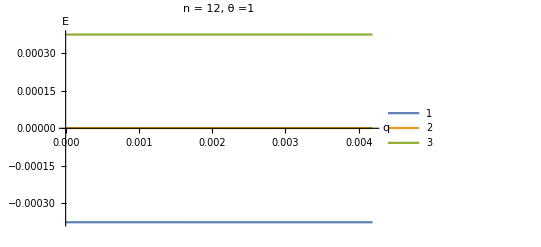

```mathematica
Plot[{E1, E2, E3},{q, 0, Subscript[k, F]}, PlotLegends->Automatic, AxesLabel->{"q", "E"}, PlotLabel->"n = 12, θ =1 "]
```

```mathematica
mat = {{0, Δ + α * q * Cos[ϕ], Conjugate[Δ] + Conjugate[α] * q * Cos[ϕ + 4 π/3]}, {Conjugate[Δ] + Conjugate[α] * q * Cos[ϕ], 0, Δ + α * q * Cos[ϕ + 2 π/3]}, {Δ + α * q * Cos[ϕ + 4 π/3], Conjugate[Δ] + Conjugate[α] * q * Cos[ϕ + 2 π/3], 0}}
```

{{0,Δ+q α Cos[ϕ],Conjugate[Δ]-q Conjugate[α] Sin[π/6-ϕ]},{Conjugate[Δ]+q Conjugate[α] Cos[ϕ],0,Δ-q α Sin[π/6+ϕ]},{Δ-q α Sin[π/6-ϕ],Conjugate[Δ]-q Conjugate[α] Sin[π/6+ϕ],0}}

```mathematica
MatrixForm[mat]
```

(0 | Δ+q α Cos[ϕ] | Conjugate[Δ]-q Conjugate[α] Sin[π/6-ϕ]
Conjugate[Δ]+q Conjugate[α] Cos[ϕ] | 0 | Δ-q α Sin[π/6+ϕ]
Δ-q α Sin[π/6-ϕ] | Conjugate[Δ]-q Conjugate[α] Sin[π/6+ϕ] | 0)

```mathematica
First[Eigenvalues[mat]]
```

Root[3 q^2 α^2 Δ-4 Δ^3+3 q^2 Conjugate[α]^2 Conjugate[Δ]-4 Conjugate[Δ]^3-q^3 α^3 Cos[ϕ]-4 q α Δ^2 Cos[ϕ]-q^3 Conjugate[α]^3 Cos[ϕ]-4 q Conjugate[α] Conjugate[Δ]^2 Cos[ϕ]-2 q^2 α^2 Δ Cos[2 ϕ]-2 q^2 Conjugate[α]^2 Conjugate[Δ] Cos[2 ϕ]-q^3 α^3 Cos[3 ϕ]-q^3 Conjugate[α]^3 Cos[3 ϕ]+2 q^2 α^2 Δ Sin[π/6-2 ϕ]+2 q^2 Conjugate[α]^2 Conjugate[Δ] Sin[π/6-2 ϕ]+q^3 α^3 Sin[π/6-ϕ]+4 q α Δ^2 Sin[π/6-ϕ]+q^3 Conjugate[α]^3 Sin[π/6-ϕ]+4 q Conjugate[α] Conjugate[Δ]^2 Sin[π/6-ϕ]+q^3 α^3 Sin[π/6+ϕ]+4 q α Δ^2 Sin[π/6+ϕ]+q^3 Conjugate[α]^3 Sin[π/6+ϕ]+4 q Conjugate[α] Conjugate[Δ]^2 Sin[π/6+ϕ]+2 q^2 α^2 Δ Sin[π/6+2 ϕ]+2 q^2 Conjugate[α]^2 Conjugate[Δ] Sin[π/6+2 ϕ]+(-6 q^2 α Conjugate[α]-12 Δ Conjugate[Δ]-4 q Δ Conjugate[α] Cos[ϕ]-4 q α Conjugate[Δ] Cos[ϕ]-2 q^2 α Conjugate[α] Cos[2 ϕ]+2 q^2 α Conjugate[α] Sin[π/6-2 ϕ]+4 q Δ Conjugate[α] Sin[π/6-ϕ]+4 q α Conjugate[Δ] Sin[π/6-ϕ]+4 q Δ Conjugate[α] Sin[π/6+ϕ]+4 q α Conjugate[Δ] Sin[π/6+ϕ]+2 q^2 α Conjugate[α] Sin[π/6+2 ϕ]) #1+4 #1^3&,1]

```mathematica
FullSimplify[Root[3 q^2 α^2 Δ-4 Δ^3+3 q^2 Conjugate[α]^2 Conjugate[Δ]-4 Conjugate[Δ]^3-q^3 α^3 Cos[ϕ]-4 q α Δ^2 Cos[ϕ]-q^3 Conjugate[α]^3 Cos[ϕ]-4 q Conjugate[α] Conjugate[Δ]^2 Cos[ϕ]-2 q^2 α^2 Δ Cos[2 ϕ]-2 q^2 Conjugate[α]^2 Conjugate[Δ] Cos[2 ϕ]-q^3 α^3 Cos[3 ϕ]-q^3 Conjugate[α]^3 Cos[3 ϕ]+2 q^2 α^2 Δ Sin[π/6-2 ϕ]+2 q^2 Conjugate[α]^2 Conjugate[Δ] Sin[π/6-2 ϕ]+q^3 α^3 Sin[π/6-ϕ]+4 q α Δ^2 Sin[π/6-ϕ]+q^3 Conjugate[α]^3 Sin[π/6-ϕ]+4 q Conjugate[α] Conjugate[Δ]^2 Sin[π/6-ϕ]+q^3 α^3 Sin[π/6+ϕ]+4 q α Δ^2 Sin[π/6+ϕ]+q^3 Conjugate[α]^3 Sin[π/6+ϕ]+4 q Conjugate[α] Conjugate[Δ]^2 Sin[π/6+ϕ]+2 q^2 α^2 Δ Sin[π/6+2 ϕ]+2 q^2 Conjugate[α]^2 Conjugate[Δ] Sin[π/6+2 ϕ]+(-6 q^2 α Conjugate[α]-12 Δ Conjugate[Δ]-4 q Δ Conjugate[α] Cos[ϕ]-4 q α Conjugate[Δ] Cos[ϕ]-2 q^2 α Conjugate[α] Cos[2 ϕ]+2 q^2 α Conjugate[α] Sin[π/6-2 ϕ]+4 q Δ Conjugate[α] Sin[π/6-ϕ]+4 q α Conjugate[Δ] Sin[π/6-ϕ]+4 q Δ Conjugate[α] Sin[π/6+ϕ]+4 q α Conjugate[Δ] Sin[π/6+ϕ]+2 q^2 α Conjugate[α] Sin[π/6+2 ϕ]) #1+4 #1^3&,1]]
```

Root[3 q^2 α^2 Δ-4 Δ^3+3 q^2 Conjugate[α]^2 Conjugate[Δ]-4 Conjugate[Δ]^3-q^3 α^3 Cos[3 ϕ]-q^3 Conjugate[α]^3 Cos[3 ϕ]+(-6 q^2 α Conjugate[α]-12 Δ Conjugate[Δ]) #1+4 #1^3&,1]